# Retrospective evaluation of school-related measures on pre-vaccination transmission dynamics of SARS-CoV-2

## Benedetta Canfora, Rey Audie Escosio, Christiaan H. van Dorp, Otilia Boldea, Marc Bonten, Ana Nunes, and Ganna Rozhnova* Corresponding author: g.rozhnova@umcutrecht.nl

## Main analysis for baseline and two counterfactual scenarios

## Global parameters

```mathematica
(* Clear *)
$HistoryLength=0;
ClearSystemCache[]
ClearAll["Global`*"]
Clear["Subscript"]
Clear["Superscript"]
Clear["Subsuperscript"]
Off[General::munfl]
SetDirectory[NotebookDirectory[]];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
```

### Packages and parameters

```mathematica
(* External packages *)
AppendTo[$Path,"../packages"];
Needs["plotting`"];
Needs["preliminaries`"];

createResultDirectories[];

(*Remove["plotting`*"]
Get["../packages/plotting.m"]*)

(* Notebook parameters *)
ifShowFigs= True;
ifExportData = False;
ifExportFigs = False;
exportFormat={".pdf",".eps"};

(* Known constants *)
(* Age groups *)
numAgeGroups = 10;
listAgeGroups= Table[k, {k, 1, numAgeGroups}];
listChildren = Range[1,3];
listAdults = Range[4,10];
groupIndex = {listChildren, listAdults};

(* Samples *)
numAllSamples = 2000;
stepSamples=20; (* 20 corresponds to 100 samples *)
listSamples=Table[i,{i,1,numAllSamples,stepSamples}];
numSamples = Length[listSamples];

(* Variables *)
numVariables=5;
varNumbers= Table[j, {j, 1, numVariables}];
eqNumbers=Table[k,{k,1,numAgeGroups numVariables}];

(* Scenarios *)
(*scenarios={"Baseline", "Scenario1", "Scenario2","Scenario1_StrictLD", "Scenario1_ExtendSchools", "Scenario2_WinterHolidays", "Scenario2_AltReductions"};*)
scenarios={"Baseline", "Scenario1", "Scenario2"};
numScenarios = Length[scenarios];
```

### Important dates and time step

```mathematica
(* Date of starting simulations: February 25, 2020 *)
timeStart=0;
(* Date of start of the pandemic: February 26, 2020 *)

(* Date of last hospitalization/last data point: January 15, 2021 *)
timeEndData = Differences[{DateObject[{2020, 02, 26}],DateObject[{2021,01,15}]}]⟦1,1⟧+1+1 ; (* Jan 15 but starting with t=1 *)


(* Integration end-time and time step *)
tStep=1;
tEnd=timeEndData;
tStart=timeStart;
times =Range[tStart,tEnd,tStep];
numTimes = Length[times];

(* Scenario time points *)
tStart1="February 25, 2020";
tEnd1="July 15, 2020";
tStart2="July 15, 2020";
tEnd2="January 16, 2021";
```

## Demography and contact matrices

### Seroprevalence data

```mathematica
totalMeanSero=2.9;
totalLowMeanSero=2.0;
totalHighMeanSero=4.2;
seroTotalDataAround = Around[totalMeanSero, {Abs[totalMeanSero - totalLowMeanSero], Abs[totalHighMeanSero-totalMeanSero]}];

seroprevalenceData=100 * Drop[Import["../data/PT_SEROPREVALENCE_DATA.csv"],1][[All,5;;7]];
seroAgeDataAround=Table[Around[seroprevalenceData[[i,1]],{seroprevalenceData[[i,1]] - seroprevalenceData[[i,2]],seroprevalenceData[[i,3]] - seroprevalenceData[[i,1]]}],{i,1,Length[seroprevalenceData]}];

seroDataMay28Around =Flatten[ {seroTotalDataAround, seroAgeDataAround}];
```

### Contact matrices from Vespignani et al.

```mathematica
(* Importing Data *)
(* https://github.com/mobs-lab/mixing-patterns *)
demographyData85=Import["../data/PT_DEMOGRAPHY_DATA_85.csv"]⟦All,2⟧;
contactDataBefore85=Import["../data/PT_CONTACT_MATRIX_TOTAL_85.csv"];
schoolContactDataBefore85=  11.41 * Import["../data/PT_CONTACT_MATRIX_SCHOOL_85.csv"];


(* Get the total contacts per participant *)
calculateTotalContsPerPar[conmat_, groupNo_] := Table[Total[conmat⟦k,All⟧],{k,groupNo}];
```

### Transforming the contact matrices from 86x86 to 10x10

```mathematica
(* Demographic data for 86+
https://www.pordata.pt/Portugal/Popula%C3%A7%C3%A3o+residente++m%C3%A9dia+anual+total+e+por+grupo+et%C3%A1rio-10 *)
demog86Plus = 316442;

(* Getting the ratio of lockdown contacts based on NL data *)
contactDataNLBefore10=Import["../data/NL_CONTACT_MATRIX_BEFORE_10.csv"];
contactDataNLAfter10=Import["../data/NL_CONTACT_MATRIX_AFTER_10.csv"];
contactRatioNL10=contactDataNLAfter10/contactDataNLBefore10;
demographyData10=Flatten[Import["../data/PT_DEMOGRAPHY_DATA_10.xlsx"]];

(* Function transforming the 1x86 age groups to 1x10 *)
transformList86to10[list85_]:=Total/@Join[Partition[list85,5]⟦1;;2⟧,Partition[list85,10]⟦2;;⟧,{list85⟦81;;⟧}];
demographyData86=Append[demographyData85, demog86Plus];
demographyData10Derived=transformList86to10[demographyData86];


(* Creating the 86x86 contact matrices *)
transformMatrix85to86[mat85_]:=Join[Join[mat85,{mat85⟦85⟧}],List/@(Join[mat85,{mat85⟦85⟧}]⟦All,85⟧ demographyData86⟦86⟧/demographyData86⟦85⟧), 2];
contactDataBefore86=transformMatrix85to86[contactDataBefore85];
schoolContactDataBefore86=transformMatrix85to86[schoolContactDataBefore85];


(* Creating the 10x10 contact matrices*)
transformMatrix86to10[mat86_] :=transformList86to10[Transpose[transformList86to10[Transpose[mat86]]] demographyData86]/demographyData10Derived;
fileContactBefore10="../data/RES_PT_CONTACT_MATRIX_BEFORE_10.csv";
fileContactAfter10="../data/RES_PT_CONTACT_MATRIX_AFTER_10.csv";
fileSchoolBefore10="../data/RES_PT_CONTACT_MATRIX_SCHOOL_10.csv";
If[FileExistsQ[fileContactBefore10]&&FileExistsQ[fileContactAfter10]&&FileExistsQ[fileSchoolBefore10],

contactDataBefore10=Import[fileContactBefore10, "Table","FieldSeparators"->"\t"];
contactDataAfter10=Import[fileContactAfter10, "Table","FieldSeparators"->"\t"];
schoolContactDataBefore10=Import[fileSchoolBefore10, "Table","FieldSeparators"->"\t"];
,

contactDataBefore10=transformMatrix86to10[contactDataBefore86];
contactDataAfter10=contactDataBefore10 * contactRatioNL10 ;
schoolContactDataBefore10=transformMatrix86to10[schoolContactDataBefore86];

Export[fileContactBefore10,contactDataBefore10, ];
Export[fileContactAfter10,contactDataAfter10];
Export[fileSchoolBefore10,schoolContactDataBefore10];
]

(* Get the total contacts per participant *)
calculateContactsAgeGroupsBefore=calculateTotalContsPerPar[contactDataBefore10, numAgeGroups];
calculateSchoolContactsAgeGroupsBefore=calculateTotalContsPerPar[schoolContactDataBefore10, numAgeGroups];
calculateContactsAgeGroupsAfter=calculateTotalContsPerPar[contactDataAfter10, numAgeGroups];

(* Get the average contacts per participant *)
calculateAverageContactRateBefore=Sum[calculateContactsAgeGroupsBefore⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];
calculateAverageContactRateSchoolsBefore=Sum[calculateSchoolContactsAgeGroupsBefore⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];
calculateAverageContactRateAfter=Sum[calculateContactsAgeGroupsAfter⟦k⟧ *demographyData10⟦k⟧/Total[demographyData10],{k,listAgeGroups}];
```

## Hospitalization data and estimated parameters

### Estimated parameters

```mathematica
(* Importing estimated parameters *)
estimatesData=Import["../data/PARAMETER_ESTIMATES.csv"];
headerParameters=estimatesData⟦1⟧;
estimatesData=Drop[estimatesData,1];
```

```mathematica
(* Total population *)
totalPop=Table[Subscript[NN,k]->demographyData10[[k]],{k,listAgeGroups}];

(* Contact matrix variables *)
contactRates=Flatten[Table[{Subscript[b,{k,l}]->contactDataBefore10[[k,l]],Subscript[a,{k,l}]->contactDataAfter10[[k,l]],Subscript[s,{k,l}]->schoolContactDataBefore10[[k,l]]},{k,1,numAgeGroups},{l,1,numAgeGroups}]];

(* Table for all parameters; also assigning variables *)
parametersComplete[sample_Integer]:=
Module[{est},
est=estimatesData[[sample]];
Flatten[{contactRates,totalPop,
(* Age-independent parameters *)
ϵ->est[[1]],ζ->est[[2]],α->est[[18]],γ->est[[19]],
(* Hospitalization rate *)
Table[Subscript[ν,k]->est[[2+k]],{k,1,numAgeGroups}],(* Initial conditions *)Table[{Subscript[S0,k]->1-est[[13]],Subscript[EE0,k]->0.5*est[[13]],Subscript[II0,k]->0.5*est[[13]],Subscript[R0,k]->0,Subscript[H0,k]->0},{k,listAgeGroups}],
(* Susceptibility *)
Table[Subscript[β,k]->est[[14]],{k,1,3}],Table[Subscript[β,k]->est[[15]],{k,4,7}],Table[Subscript[β,k]->est[[16]],{k,8,10}],
(* Logistic function parameters *){Subscript[xx,0]->est[[20]],Subscript[K,0]->est[[21]],Subscript[xx,1]->est[[22]],Subscript[K,1]->est[[23]],Subscript[xx,2]->est[[24]],Subscript[K,2]->est[[25]],Subscript[xx,3]->est[[26]],Subscript[K,3]->est[[27]],Subscript[xx,4]->est[[28]],Subscript[K,4]->est[[29]]},
{Subscript[u,1]->est[[30]],Subscript[u,2]->est[[31]],Subscript[u,3]->est[[32]],Subscript[u,4]->est[[33]]}}]];

(* Sampled parameters *)
parametersCompleteSampled=Table[parametersComplete[i],{i,1,numAllSamples,stepSamples}];
```

### Hospitalization data

```mathematica
(* Importing data *)
hospitalizationData=Import["../data/PT_HOSPITALIZATION_DATA.csv"];
hospitalizationData=Drop[hospitalizationData,1];
hospitalizationDataTotal =Total[hospitalizationData, {2}];
hospitalizationDataGrouped = {Total[hospitalizationData[[All, 4;;10]], {2}], Total[hospitalizationData[[All, 1;;3]], {2}]};


(* Transition dates and their respective quantiles *)transitionDates=Table[DayPlus[{2020,02,25}, IntegerPart[Median[estimatesData⟦All,index⟧]]],{index,Range[20,28,2]}]; 
transitionDatesQuantiles025=Table[DayPlus[{2020,02,25}, IntegerPart[Quantile[estimatesData⟦All,index⟧,0.025]]],{index,Range[20,28,2]}]; 
transitionDatesQuantiles975=Table[DayPlus[{2020,02,25}, IntegerPart[Quantile[estimatesData⟦All,index⟧,0.975]]],{index,Range[20,28,2]}]; 
(* Range[20,28,2] are the indices for transition dates *)
```

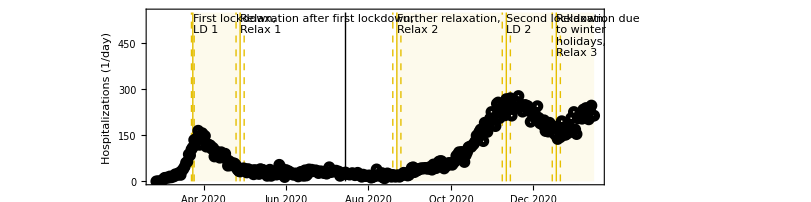

```mathematica
(* Plotting the diagram with the hospitalization data *)
figDiag = plotDiagram[hospitalizationData, ticksVisible];
exportFigs[figDiag, "Fig2"];
```

```mathematica
transitionDates
```

{Tue 24 Mar 2020,Tue 28 Apr 2020,Sat 22 Aug 2020,Wed 11 Nov 2020,Fri 18 Dec 2020}

## Equations and variables

### Expressions for contact matrices

```mathematica
contactMatrixBaseline[t_]:=
(Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));


(* SCENARIO 1 *)
(* Schools remained open during LD1 before transitioning to the first relaxation of measures *)
contactMatrixScenario1[t_]:=
(Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) (ζ Subscript[a,{k,l}] + Subscript[s,{k,l}])(1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));


(* SCENARIO 2 *)
(* Schools remained closed after the 2020 summer holidays spanning Relax 2, LD 2, and Relax 3 *)
contactMatrixScenario2[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-Subscript[u, 2]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-Subscript[u, 3]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-Subscript[u, 4] Subscript[s,{k,l}]);
```

```mathematica
(* ADDITIONAL SENSITIVITY ANALYSES *)
(* Scenario 1.1: Strict LD across counterfactual periods *)
(* 106 corresponds to June 10, start of school holidays*)
contactMatrixScenario1StrictLD[t_]:=
((Subscript[b,{k,l}]-Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
Subscript[s,{k,l}] (1-1/(1+Exp[-10 (t-106)]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));

(* Scenario 1.2: Extended school opening after lockdown *)
(* 106 corresponds to June 10, start of school holidays*)
contactMatrixScenario1ExtendSchools[t_]:=
((Subscript[b,{k,l}]-Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
Subscript[s,{k,l}] (1-1/(1+Exp[-10 (t-106)]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]));

(* Scenario 2.1: School winter holidays *)
contactMatrixScenario2WinterHolidays[t_]:=
Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-Subscript[u, 2]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-Subscript[u, 3]  Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]); 

(* Scenario 2.2: Alternative reductions in school-based contacts *)
(* Note that zetaSchools is obtained by calibration, and not imported above *)
contactMatrixScenario2AltReductions[t_]:=
(Subscript[b,{k,l}] (1-1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]))+
1/(1+Exp[-Subscript[K, 0](t-Subscript[xx, 0])]) ζ Subscript[a,{k,l}](1-1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]))+
1/(1+Exp[-Subscript[K, 1](t-Subscript[xx, 1])]) (Subscript[u, 1] Subscript[b,{k,l}]+(1-Subscript[u, 1])ζ Subscript[a,{k,l}]) (1-1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]))+
1/(1+Exp[-Subscript[K, 2](t-Subscript[xx, 2])]) (Subscript[u, 2] Subscript[b,{k,l}]+(1-Subscript[u, 2])ζ Subscript[a,{k,l}]-zetaSchools Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]))+
1/(1+Exp[-Subscript[K, 3](t-Subscript[xx, 3])]) (Subscript[u, 3] Subscript[b,{k,l}]+(1-Subscript[u, 3])ζ Subscript[a,{k,l}]-zetaSchools Subscript[s,{k,l}]) (1-1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]))+
1/(1+Exp[-Subscript[K, 4](t-Subscript[xx, 4])]) (Subscript[u, 4] Subscript[b,{k,l}]+(1-Subscript[u, 4])ζ Subscript[a,{k,l}]-zetaSchools Subscript[s,{k,l}]));
```

### Model equations

```mathematica
(* Table of equations *)Table[{eq[Intervention_][1,k]:=Subscript[S,k]'[t]== - Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t],eq[Intervention_][2,k]:=Subscript[EE,k]'[t]== Subscript[λ,k][Intervention][t] Subscript[β,k] Subscript[S,k][t]-α Subscript[EE,k][t],
eq[Intervention_][3,k]:=Subscript[II,k]'[t]== α Subscript[EE,k][t]-(γ +Subscript[ν,k]) Subscript[II,k][t],
eq[Intervention_][4,k]:=Subscript[R,k]'[t]==γ Subscript[II,k][t],
eq[Intervention_][5,k]:=Subscript[H,k]'[t]==Subscript[ν,k] Subscript[II,k][t]},{k,listAgeGroups}];
NNtot=Sum[Subscript[NN,k],{k,listAgeGroups}];
```

```mathematica
(* The contact matrix to use *)
contactMatrix["Baseline",t_]:=contactMatrixBaseline[t];
contactMatrix["Scenario1",t_]:=contactMatrixScenario1[t];
contactMatrix["Scenario2",t_]:=contactMatrixScenario2[t];
contactMatrix["Scenario1_StrictLD",t_]:=contactMatrixScenario1StrictLD[t];
contactMatrix["Scenario1_ExtendSchools",t_]:=contactMatrixScenario1ExtendSchools[t];
contactMatrix["Scenario2_WinterHolidays",t_]:=contactMatrixScenario2WinterHolidays[t];
contactMatrix["Scenario2_AltReductions",t_]:=contactMatrixScenario2AltReductions[t];
contactMatrix[_,_]:=$Failed; (* Fallback error catch *)
```

```mathematica
(* Final table of equations considering the interventions as the argument *)
eqsList[intervention_String]:=
Module[{lambda},
(* Force of infection *)
lambda[k_,t_]:=ϵ*Sum[contactMatrix[intervention,t]*Subscript[II,l][t]/Subscript[NN,l],{l,listAgeGroups}];

Flatten[{
Table[Subscript[S,k]'[t]==-lambda[k,t]*Subscript[β,k]*Subscript[S,k][t],{k,listAgeGroups}],
Table[Subscript[EE,k]'[t]==lambda[k,t]*Subscript[β,k]*Subscript[S,k][t]-α*Subscript[EE,k][t],{k,listAgeGroups}],Table[Subscript[II,k]'[t]==α*Subscript[EE,k][t]-(γ+Subscript[ν,k])*Subscript[II,k][t],{k,listAgeGroups}],
Table[Subscript[R,k]'[t]==γ*Subscript[II,k][t],{k,listAgeGroups}],
Table[Subscript[H,k]'[t]==Subscript[ν,k]*Subscript[II,k][t],{k,listAgeGroups}]}]]
```

### Variables

```mathematica
(* List of variables for each compartment and their totals *)
varsS=Table[Subscript[S,k][t],{k,listAgeGroups}];
varsEE=Table[Subscript[EE,k][t],{k,listAgeGroups}];
varsII=Table[Subscript[II,k][t],{k,listAgeGroups}];
varsR=Table[Subscript[R,k][t],{k,listAgeGroups}];
varsH=Table[Subscript[H,k][t],{k,listAgeGroups}];

vars=Join[varsS,varsEE,varsII,varsR,varsH];
varsList=Flatten[vars];

(* Indices of the compartments in all of the equations (will come in handy in NGM) *)
eqNumbersSusceptible = eqNumbers[[1 ;; numAgeGroups]];
eqNumbersExposed = eqNumbers[[numAgeGroups + 1 ;; 2 numAgeGroups]];
eqNumbersInfectious = eqNumbers[[2 numAgeGroups + 1 ;; 3 numAgeGroups]];

(* Expression for the daily hospitalizations*)
hospVars=Table[Subscript[ν,k] (Subscript[II,k][t]),{k,listAgeGroups}];
```

### Solving the model

```mathematica
(* Initial conditions *)
ICs=Table[ic[j,k],{j,varNumbers},{k,listAgeGroups}];
ICsList=Flatten[Flatten[ICs]];
(* Particularly for the compartments wherein we initially defined them as percentages from the total population (since N is constant through time)*)Table[ic[1,k]=Subscript[S0,k] Subscript[NN,k]==Subscript[S,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[2,k]=Subscript[EE0,k] Subscript[NN,k]==Subscript[EE,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[3,k]=Subscript[II0,k] Subscript[NN,k]==Subscript[II,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[4,k]=Subscript[R0,k] Subscript[NN,k]==Subscript[R,k][t]/.{t->tStart},{k,listAgeGroups}];
Table[ic[5,k]=Subscript[H0,k] Subscript[NN,k]==Subscript[H,k][t]/.{t->tStart},{k,listAgeGroups}];

(* Function solving the model *)
solution[intervention_,pars_]:=NDSolve[Join[eqsList[intervention],ICsList]/.pars,
varsList,{t,tStart,tEnd}, Method->"StiffnessSwitching"];
(* and a for loop for each sample to solve it (this is still a function!) *)
solutionsForLoop[i_]:=Table[solution[scenarios[[i]],parametersCompleteSampled[[j]]],{j,1,Length[listSamples]}];
(* and finally importing/exporting them *)
solutionsScenarios = importExportScenarioResults["SOLUTIONS", solutionsForLoop, "solutions"];
```

```mathematica
(* We aim to evaluate these solutions of the model with respect to certain trajectories (hospitalizations and susceptible population for seroprevalence) *)
trajectoriesVarForLoop[var_, i_, label_]:= 
Table[Table[Table[Evaluate[
(If[label === "SUSCEPTIBLE",
(If[k==1,(demographyData10⟦1⟧-86579)/demographyData10⟦1⟧,1] var⟦k⟧)+ If[k==1,86579,0],
var⟦k⟧]/.parametersCompleteSampled⟦j⟧)/.First@solutionsScenarios[[i]]⟦j⟧],
{t,tStart,tEnd,tStep}],
{j,1,Length[listSamples]}],
{k,listAgeGroups}]; 
importExport4Trajectories[var_, label_] := Module[{func},
func[i_] := trajectoriesVarForLoop[var, i,label];
importExportScenarioResults[label, func, "solutions"]];

(* and since we will regroup them according to age-specific or total populations, we need to sum them accordingly *)
summingGroups4Scenarios[variable_, index_] := Transpose[Table[Map[Total[#[[index[[i]], All, All]], {1}] &, variable], {i, 1, Length[index]}]];
```

## Analysis

### Hospitalizations

```mathematica
(* Hospitalizations for the 10 age groups, for youth and adults, and for the total population *)hospitalizationScenarios=importExport4Trajectories[hospVars, "HOSPITALIZATION"];
hospitalizationScenariosGrouped = summingGroups4Scenarios[hospitalizationScenarios, groupIndex];
hospitalizationScenariosTotal = summingGroups4Scenarios[hospitalizationScenarios, {Range[1, 10]}];

(* Simulating a negative binomial distribution, we regenerate the hospitalizations *)
NBDReparameterized[m_,f_]:=NegativeBinomialDistribution[f,f/(f+m)];
hospSimulated[var_]:=Table[If[var⟦k⟧⟦sample⟧⟦t⟧>0,RandomVariate[NBDReparameterized[var⟦k⟧⟦sample⟧⟦t⟧,rOverDisp[listSamples⟦sample⟧]]],0],{k,listAgeGroups},{sample,1,Length[listSamples]},{t,1,Dimensions[var]⟦3⟧}];
hospitalizationSimulatedLoop[label_] := Module[{func},
func[i_] := hospSimulated[hospitalizationScenarios[[i]]];
     importExportScenarioResults[label, func, "solutions"]];

(* Getting simulated (noised) hospitalizations for the 10 age groups, for youth and adults, and for the total population *)hospitalizationSimulatedScenarios = hospitalizationSimulatedLoop["HOSPNEGBIN"];
hospitalizationSimulatedScenariosGrouped = summingGroups4Scenarios[hospitalizationSimulatedScenarios, groupIndex];
hospitalizationSimulatedScenariosTotal = summingGroups4Scenarios[hospitalizationSimulatedScenarios, {Range[1, 10]}];
```

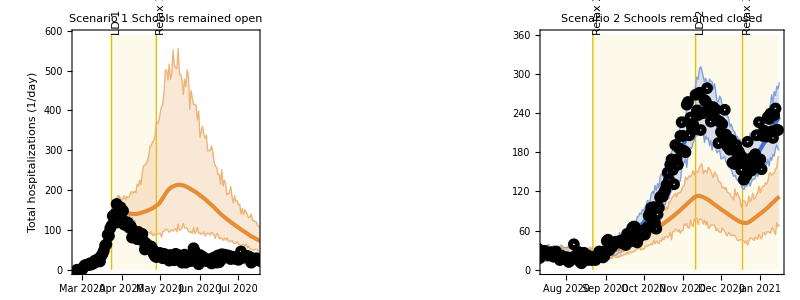
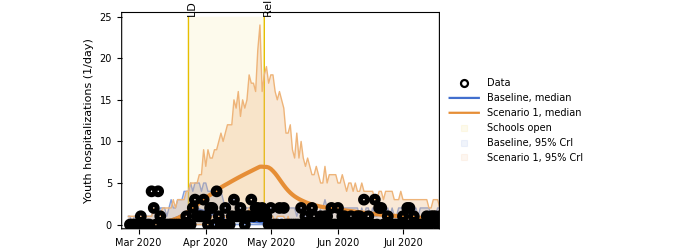
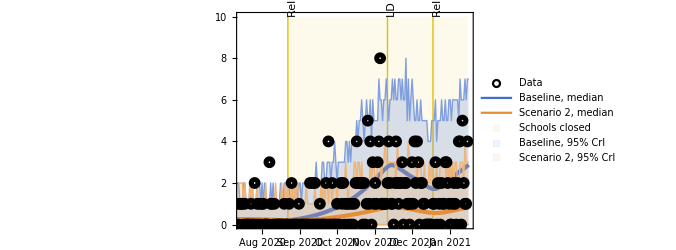
-Graphics-
-Graphics- | -Graphics-

```mathematica
(* Plotting *)
(* Scatter plot for the hospitalization data *)scatterPlotHospData = DateListPlot[Total[hospitalizationData,{2}], "February 26, 2020", Joined->False, PlotTheme -> "Web",PlotMarkers->{Graphics[{Black,Style[Circle[],Thickness[0.25]]}],5}];
scatterPlotHospDataChild = DateListPlot[Total[hospitalizationData[[All, 1;;3]],{2}], "February 26, 2020", Joined->False, PlotTheme -> "Web",PlotMarkers->{Graphics[{Black,Style[Circle[],Thickness[0.25]]}],5}];

(* For hospitalizations, we use the median of the solutions (not noised) and the quantiles of the simulated (noised) *)hospSimulTotal2Plot = {hospitalizationSimulatedScenariosTotal[[1,1, All, All]],
hospitalizationSimulatedScenariosTotal[[2,1, All, All]],
hospitalizationSimulatedScenariosTotal[[3,1, All, All]]};
hospTot2Plot = {hospitalizationScenariosTotal[[1,1, All, All]],
hospitalizationScenariosTotal[[2,1, All, All]],
hospitalizationScenariosTotal[[3,1, All, All]]};
hospSimulYouth2Plot = {hospitalizationSimulatedScenariosGrouped[[1,1, All, All]],
hospitalizationSimulatedScenariosGrouped[[2,1, All, All]],
hospitalizationSimulatedScenariosGrouped[[3,1, All, All]]};
hospYouth2Plot={hospitalizationScenariosGrouped[[1,1, All, All]],
hospitalizationScenariosGrouped[[2,1, All, All]],
hospitalizationScenariosGrouped[[3,1, All, All]]};

figHospTotal = plotScenarioTrajectories[hospSimulTotal2Plot, "Total hospitalizations (1/day)",{"Scenario 1\nSchools remained open","Scenario 2\nSchools remained closed"},{ticksInvisible, ticksInvisible},{{0,590},{0,360}},{"a", "c"}, "lefter",scatterPlotHospData, 
hospTot2Plot];
figHospYouth = plotScenarioTrajectories[hospSimulYouth2Plot, "Youth hospitalizations (1/day)",{"", ""},{ticksVisible, ticksVisible},{{0,25},{0,10}},{"b", "d"}, "lefter",scatterPlotHospDataChild, 
hospYouth2Plot, False, "hosp"];


figHospTotalYouth = Grid[{{figHospTotal}, {figHospYouth}}];
exportFigs[figHospTotalYouth, "Fig3"];
```

### Seroprevalence

```mathematica
(* Susceptible population for the 10 age groups, for youth and adults, and for the total population *)susceptibleScenarios =importExport4Trajectories[varsS, "SUSCEPTIBLE"];
susceptibleScenariosGrouped = summingGroups4Scenarios[susceptibleScenarios, groupIndex];
susceptibleScenariosTotal = summingGroups4Scenarios[susceptibleScenarios, {Range[1, 10]}];

(* Calculating the seroprevalence for the total population *)
seroprevalenceScenariosTotal = 100-100susceptibleScenariosTotal/Total[demographyData10];
(* for youth and adults *)
seroprevalenceScenariosGrouped = ConstantArray[0, {3,2,100,327}];
Table[seroprevalenceScenariosGrouped[[All, k, All, All]]=
100-100susceptibleScenariosGrouped[[All,k,All,All]]/Total[demographyData10[[groupIndex[[k]]]]];, {k ,1,2}];
(* and for the 10 age groups *)
seroprevalenceScenarios = ConstantArray[0, {3,10,100,327}];
Table[seroprevalenceScenarios[[All, k, All, All]]=
100-100susceptibleScenarios[[All,k,All,All]]/Total[demographyData10[[k]]];, {k ,1,numAgeGroups}];
```

```mathematica
(* Assuming that the susceptible population is proportional to the total population, the [1,5) population percentage can be computed as follows *)susceptible1to5Percent = Total[demographyData85[[2;;5]]]/Total[demographyData85[[1;;5]]];
susceptibleScenariosWithoutBabies = susceptibleScenarios;
susceptibleScenariosWithoutBabies[[All,1,All,All]]=susceptible1to5Percent*susceptibleScenarios[[All,1,All,All]];
demographyData10WithoutBabies = demographyData10;
demographyData10WithoutBabies[[1]] =susceptible1to5Percent* demographyData10[[1]];

regroupIndex = {{1,2}, {3},{4,5}, {6,7}, {8,9,10}};
susceptibleScenariosRegrouped4Sero = summingGroups4Scenarios[susceptibleScenariosWithoutBabies,regroupIndex ];
seroprevalenceScenariosRegrouped = ConstantArray[0, {3,5,100,327}];
Table[seroprevalenceScenariosRegrouped[[All, k, All, All]]=
100-100susceptibleScenariosRegrouped4Sero[[All,k,All,All]]/Total[demographyData10WithoutBabies[[regroupIndex[[k]]]]];, {k ,1,5}];
```

### Infections

```mathematica
infIncidenceVars=Table[α (Subscript[EE,k][t]),{k,listAgeGroups}];
incidencesScenarios=importExport4Trajectories[infIncidenceVars, "INCIDENCE"];
```

```mathematica
incidCumu = Transpose[Accumulate[Transpose[Total[incidencesScenarios, {2}],{2,3,1} ]], {3,1,2}];
(*Print[Median[incidCumu[[1,All,93]]]]
Print[Quantile[incidCumu[[1,All,93]],0.025]]
Print[Quantile[incidCumu[[1,All,93]],0.975]]*)
```

### Contacts

```mathematica
(* Evaluating the contact expressions *)
trajectoriesContacts[i_, t_, sample_]:=Table[Table[contactMatrix[scenarios[[i]],t]/.parametersCompleteSampled⟦sample⟧/.contactRates, {l, 1, numAgeGroups}], {k, 1, numAgeGroups}];
importExport4Contacts[label_] := Module[{func},
func[i_] := Table[Table[trajectoriesContacts[i, t, j],{t,tStart,tEnd,tStep}],{j,1,Length[listSamples]}];
importExportScenarioResults[label, func, "solutions"]];
(* and saving them as CONTACT files (these are still contact matrices) *)
contactMatricesScenarios = importExport4Contacts["CONTACTS"];
```

```mathematica
(* Getting the average contacts *)
gettingAverageContacts[startrange_,endrange_]:=
Module[{summedRows,specificAges,demographyPercentage},
summedRows=Total[contactMatricesScenarios,{5}];
specificAges=summedRows[[All,All,All,startrange;;endrange]];
demographyPercentage=demographyData10[[startrange;;endrange]]/Total[demographyData10[[startrange;;endrange]]];

specificAges.demographyPercentage];

(* Getting the average contacts for total, and age-specific groups *)
averageContactsTotal= gettingAverageContacts[1,10];
averageContactsYouth= gettingAverageContacts[1,3];
averageContactsAdults =gettingAverageContacts[4,10];
```

### Reproduction number

```mathematica
(* The next generation matrix for each scenario *)
NGM= Table[Table[((-1/D[eqsList[scenarios[[i]]]⟦p,2⟧,varsList⟦p⟧] D[eqsList[scenarios[[i]]]⟦k,2⟧,varsList⟦p⟧])),
{k,eqNumbersExposed},{p,eqNumbersInfectious}], {i, 1, Length[scenarios]}];

(* Substituting values to the next generation matrices *)
substituteNGM[scenNum_, sample_, time_] :=
((NGM[[scenNum]]/. (First@solutionsScenarios[[scenNum]][[sample]])[[eqNumbersSusceptible]]) /. parametersCompleteSampled[[sample]]) /. t -> time;
NGMForLoop[i_] :=Table[Table[substituteNGM[i, j, t], {t,tStart,tEnd,tStep}],{j,1,Length[listSamples]}];
NGMScenarios = importExportScenarioResults["NGM", NGMForLoop, "analysis"];
```

```mathematica
(* Obtaining the reproduction number and the respective eigenvectors *)
eigenAllFirst[matrix_] := Module[{valRight, valLeft}, 
valRight = Eigensystem[matrix, 1];
valLeft = Eigensystem[Transpose[matrix], 1]; 
{valRight[[1]][[1]], 
valRight[[2]][[1]],
valLeft[[2]][[1]]}];
RtForLoop[i_] :=Table[Table[eigenAllFirst[NGMScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
RtScenarios = importExportScenarioResults["EIGEN", RtForLoop, "analysis"];
```

### Cumulative elasticities

```mathematica
(* The remaining analyses are done numerically (and not symbolically) *)
(* Sensitivity matrices *)
sensMatrix[eigen_]:=
Module[{eigenRight, eigenLeft},
eigenRight = eigen[[2]];
eigenLeft = eigen[[3]];Outer[Times,eigenLeft,eigenRight]/Dot[eigenLeft, eigenRight]];
sensForLoop[i_] :=Table[Table[sensMatrix[RtScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
sensScenarios = importExportScenarioResults["SENSITIVITY", sensForLoop, "analysis"];

(* Elasticity matrices *)
elasMatrix[eigen_, NGM_, sens_] := 
Module[{R},
R = eigen[[1]];
NGM * sens / R];
elasForLoop[i_] :=Table[Table[elasMatrix[RtScenarios[[i, j, t]], NGMScenarios[[i, j, t]], sensScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
elasScenarios = importExportScenarioResults["ELASTICITY", elasForLoop, "analysis"];

(* Cumulative elasticities *)
cumuElasMatrix[elas_] :=
Total[elas,{1}];
cumuElasForLoop[i_] := Table[Table[cumuElasMatrix[elasScenarios[[i, j, t]]], {t,1, numTimes}],{j,1,Length[listSamples]}];
cumuElasScenarios = importExportScenarioResults["CUMUELAS", cumuElasForLoop, "analysis"];

(* Adding cumulative elasticities for age-specific groups (youth and adults) *)
cumuElasGroupedScenarios = Table[Table[Total[cumuElasScenarios[[scen]][[sample]][[time]][[groupIndex[[i]]]]], {i, 1, Length[groupIndex]}], {scen, 1, Length[scenarios]}, {sample, 1, Length[listSamples]}, {time, 1, numTimes}];
```

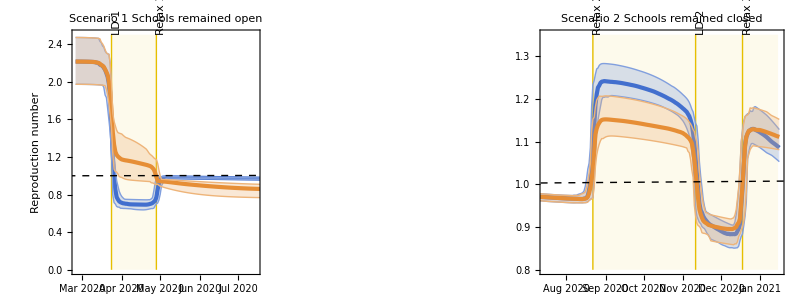
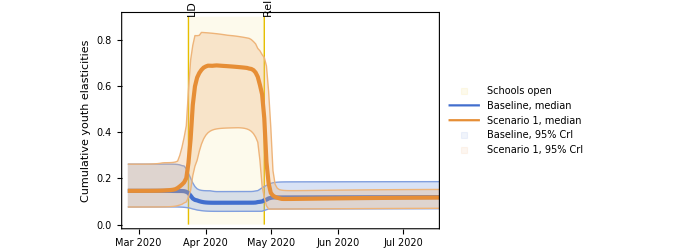
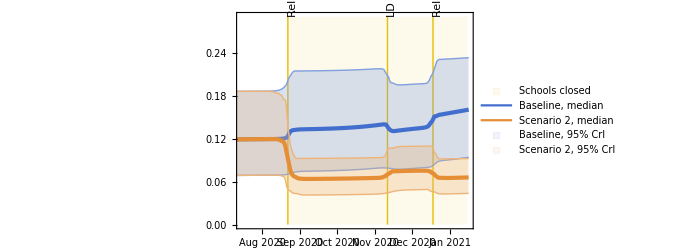
-Graphics-
-Graphics- | -Graphics-

```mathematica
(* Plotting *)
Rt1Line = Graphics[{Dashed,Black,InfiniteLine[{AbsoluteTime["February 26, 2020"],1},{AbsoluteTime["January 15, 2020"],1}]}];

Rt2Plot ={RtScenarios[[1,All,All,1]],
RtScenarios[[2,All,All,1]],
RtScenarios[[3,All,All,1]]};
cumuElas2Plot = {cumuElasGroupedScenarios[[1,All,All,1]],
cumuElasGroupedScenarios[[2,All,All,1]],
cumuElasGroupedScenarios[[3,All,All,1]]};

figRt = plotScenarioTrajectories[Rt2Plot, "Reproduction number",{"Scenario 1\nSchools remained open","Scenario 2\nSchools remained closed"},{ticksInvisible, ticksInvisible},{{0,2.5},{0.8,1.35}}, {"a", "c"}, "righter", Rt1Line];
figCumuElas = plotScenarioTrajectories[cumuElas2Plot,"Cumulative youth elasticities",{"",""},{ticksVisible,ticksVisible},{{0,0.9},{0, 0.29}},{"b", "d"}, "righter", Graphics[], {{},{},{}}, False, "elas"];

figRtCumuElasChild = Grid[{{figRt}, {figCumuElas}}];
exportFigs[figRtCumuElasChild, "Fig4"];
```

## Supplementary figures for the two scenarios

### Timeline of interventions

```mathematica
baseDate = DateObject[{2020, 2, 25}];

priorsTVals = {RandomVariate[NormalDistribution[22,7],5000],
RandomVariate[NormalDistribution[69,7],5000],
RandomVariate[NormalDistribution[203,7],5000],
RandomVariate[NormalDistribution[254,7],5000],
RandomVariate[NormalDistribution[304,7],5000]};
priorsTValsDates=Map[baseDate+Quantity[#,"Days"]&,priorsTVals];
posteriorsTVals = {estimatesData⟦All,20⟧,estimatesData⟦All,22⟧+2.94/estimatesData[[All,23]],estimatesData⟦All,24⟧,estimatesData⟦All,26⟧,estimatesData⟦All,28⟧};
posteriorsTValsDates=Map[baseDate+Quantity[#,"Days"]&,posteriorsTVals];

plotRanges={{0,50},{50,150},{170,220},{230,280},{280,350}};
plotRangesDates=Map[baseDate+Quantity[#,"Days"]&,plotRanges];
```

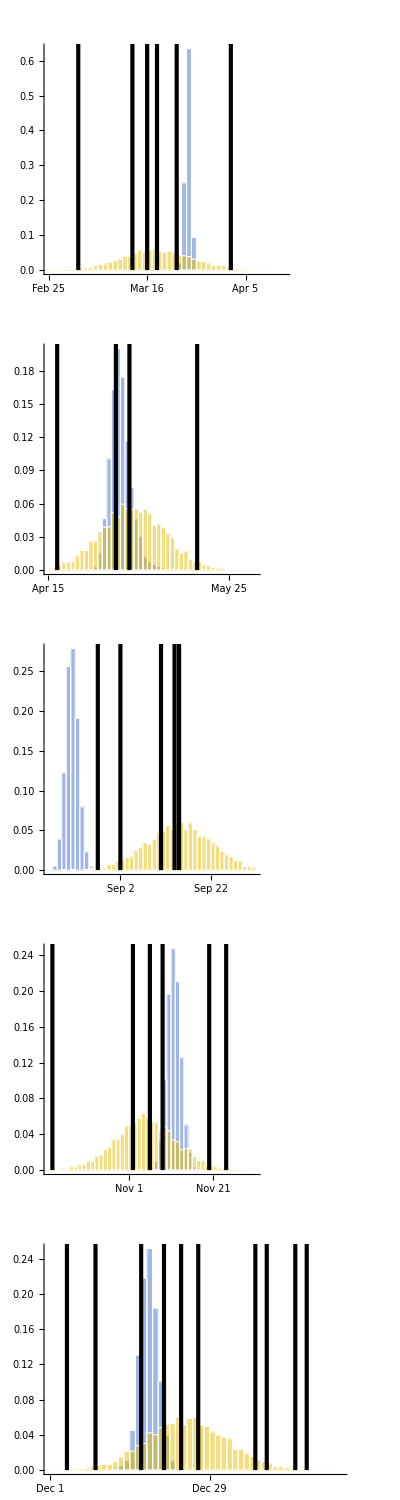
Probability | -Graphics-

```mathematica
dates2PointMajor = {{"Mar 2, 2020",  "March 18, 2020", "March 22, 2020"},
{"May 3, 2020", "May 18, 2020"},
{"Sep 15, 2020"},
{"Oct 14, 2020","Nov 9, 2020", "Nov 24, 2020"},
{"Dec 21, 2020", "Dec 27, 2020"}};
dates2AnnotateMajor = {{"0.A\nFirst confirmed case", "0.D\nDeclaration\nof State of\nEmergency", "0.E\nImplementation of\nState of Emergency"},
{"1.C\nDeclaration of\ntransition to\nState of Calamity",
"1.D\nResumption of\nsome in-person classes"},
{"2.F\nImplementation of\nState of Contingency"},
{"3.A\nImplementation of\nState of Calamity", 
"3.D\nImplementation of\nState of Emergency",
"3.F\nImplementation of\nextension of\nState of Emergency"},
{"4.D\nFirst\nAlpha\nvariant\ncase",
"4.F\nStart of\nvaccination\nprograms"}};
pointsToPlotMajor=Map[DateObject,dates2PointMajor,{2}];

dates2PointMinor = {{"Mar 13, 2020", "Mar 16, 2020", "April 2, 2020"},
{"Apr 17, 2020", "Apr 30, 2020"},
{"Aug 14, 2020", "Aug 28, 2020", "Sep 2, 2020", "Sep 11, 2020", "Sep 14, 2020"},
{"Nov 2, 2020", "Nov 6, 2020", "Nov 20, 2020"},
{"Dec 4, 2020", "Dec 9, 2020",  "Dec 17, 2020","Dec 24, 2020","Jan 6, 2021", "Jan 8, 2021", "Jan 13, 2021", "Jan 15, 2021"}};
dates2AnnotateMinor = {{" 0.B", " 0.C", " 0.F"},
{" 1.A", " 1.B"},
{" 2.A", " 2.B", " 2.C"," 2.D"," 2.\n E" },
{" 3.B", " 3.C", " 3.E"},
{" 4.A", " 4.B", " 4.C", " 4.E"," 4.G", " 4.H", " 4.I", " 4.J"}};
pointsToPlotMinor=Map[DateObject,dates2PointMinor,{2}];


figT=Table[
Module[
{plotPadding, plotRange,dailyBinSpec, plotLimits,yLimits,verticalLinesMajor,verticalLinesMinor,combinedHists,textAnnotations},
plotPadding =0.2;
plotRange=plotRangesDates[[i]];

dailyBinSpec=DateRange[plotRange[[1]],plotRange[[2]],Quantity[1,"Day"]];

combinedHists = Show[
DateHistogram[posteriorsTValsDates[[i]],
{dailyBinSpec},"Probability",
AspectRatio->0.2,FrameStyle->Directive[Black,Small],ChartStyle->Directive[colorBlue, Opacity[0.5]],ChartBaseStyle->EdgeForm[{Thick,White,Opacity[1]}],BaseStyle->{FontSize->sizeFontBig}
],
DateHistogram[priorsTValsDates[[i]],
{dailyBinSpec},"Probability",
ChartStyle->Directive[colorYellowBright, Opacity[0.5]],ChartBaseStyle->EdgeForm[{Thick,White,Opacity[1]}]
],
PlotRange->All, PlotTheme->"Web",ImageSize->1000];
plotLimits=PlotRange[combinedHists];
	yLimits=plotLimits[[2]];

combinedHists = Show[combinedHists, PlotRangePadding->{Automatic,{0,yLimits[[2]]*plotPadding}}];

	verticalLinesMajor=MapThread[{
Directive[Thickness[0.003],Black],
Line[{{#1//AbsoluteTime,0},{#1//AbsoluteTime,yLimits[[2]]+yLimits[[2]]*plotPadding}}],
Text[#2,{#1//AbsoluteTime,yLimits[[2]]+yLimits[[2]]*plotPadding},{-1.05, 1},BaseStyle->{FontSize->sizeFontSmaller, FontColor->Black}, TextAlignment->Left]}&,{pointsToPlotMajor[[i]],dates2AnnotateMajor[[i]]}];
verticalLinesMinor=MapThread[{
Directive[Thickness[0.003],Black],
Line[{{#1//AbsoluteTime,0},{#1//AbsoluteTime,yLimits[[2]]+yLimits[[2]]*plotPadding}}],
Text[#2,{#1//AbsoluteTime,yLimits[[2]]+yLimits[[2]]*plotPadding},{-1.05, 1},BaseStyle->{FontSize->sizeFontSmaller, FontColor->Black}, TextAlignment->Left]}&,{pointsToPlotMinor[[i]],dates2AnnotateMinor[[i]]}];
Legended[Show[combinedHists,
Epilog->{verticalLinesMajor, verticalLinesMinor,
{Join[{Inset[Graphics[Text[StyleForm[parameterTXLabel[[i]],FontSize->sizeFontBig,FontColor->colorRed]]],Scaled[{0.04,0.9}]]}]}}],
If[i == 1,Placed[
Column[
{SwatchLegend[{Directive[colorYellowBright, Opacity[0.5]]},{Style["Prior",FontSize->sizeFontSmall]},BaseStyle->EdgeForm[None], LegendMarkerSize->15],SwatchLegend[{Directive[colorBlue, Opacity[0.5]]},{Style["Posterior",FontSize->sizeFontSmall]},BaseStyle->EdgeForm[None], LegendMarkerSize->15]}
],
{0.99, 0.9}],
None]]
],
{i,1,Length[posteriorsTValsDates]}
];

figPriorPost=Grid[{{Style[Rotate["Probability", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[Transpose[{figT}]]}}];
exportFigs[figPriorPost, "SFig1"];
```

### Contact matrices

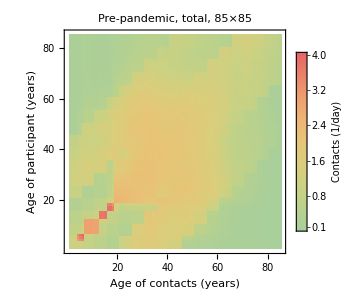
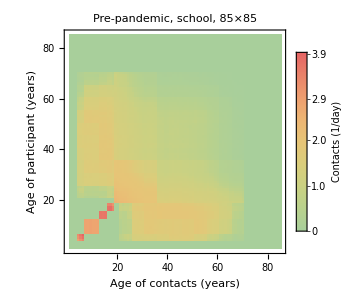
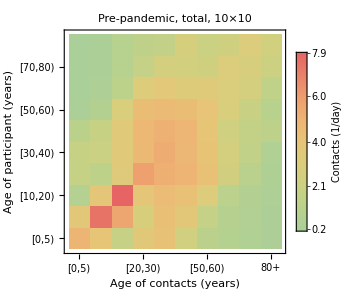
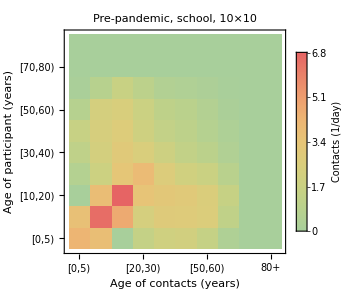
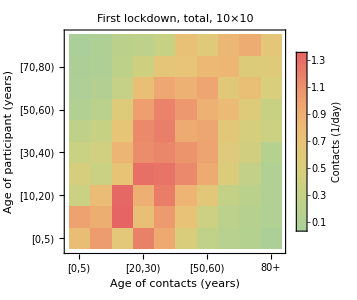
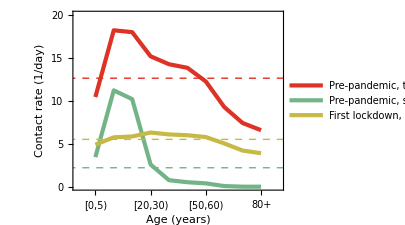
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
(* Plotting *)
mats2Plot={contactDataBefore85,schoolContactDataBefore85,contactDataBefore10,schoolContactDataBefore10,contactDataAfter10};
matTitles = {"Pre-pandemic, total, 85×85", "Pre-pandemic, school, 85×85", "Pre-pandemic, total, 10×10", "Pre-pandemic, school, 10×10",
"First lockdown, total, 10×10"};
figMats=Table[plotWithLetter[plotMatrix[mats2Plot[[matIndex]],"Rainbow",matTitles[[matIndex]],"contact"],alphabetLetters[[matIndex]]],{matIndex,1,Length[mats2Plot]}];
figF=plotWithLetter[plotThickLine[{calculateContactsAgeGroupsBefore,calculateSchoolContactsAgeGroupsBefore,calculateContactsAgeGroupsAfter},{colorRed,colorGreen,colorYellow},"","Age (years)","Contact rate (1/day)",{"Pre-pandemic, total","Pre-pandemic, schools","First lockdown, total"},"contacts",{calculateAverageContactRateBefore,calculateAverageContactRateSchoolsBefore,calculateAverageContactRateAfter},{{0,11},{0,20}},ImagePadding->{{41,Automatic},{Automatic,Automatic}}],"f"];

figConts=Grid[{{figMats[[1]],figMats[[2]]},{figMats[[3]],figMats[[4]]},{figMats[[5]],figF}}];
exportFigs[figConts, "SFig2"];
```

### Contact patterns

```mathematica
(*Epilog in DateListPlot uses AbsoluteTime for the x-axis*)
comixT1Start=AbsoluteTime[{2020,12,22}];
comixT1End=AbsoluteTime[{2021,1,7}];
comixT2Start=AbsoluteTime[{2021,1,8}];
comixT2End=AbsoluteTime[{2021,1,14}];

colorComix=Darker[Purple];

comixData10 = {{0, 0, 0, 9.9, 5.35, 6.03, 15.75, 3.41, 0, 3.25},
{0, 0, 0, 4.93, 4.47, 6.28, 6.12, 2.84, 0, 2.01}};
comixDataAdults = {8.19, 5.03};
```

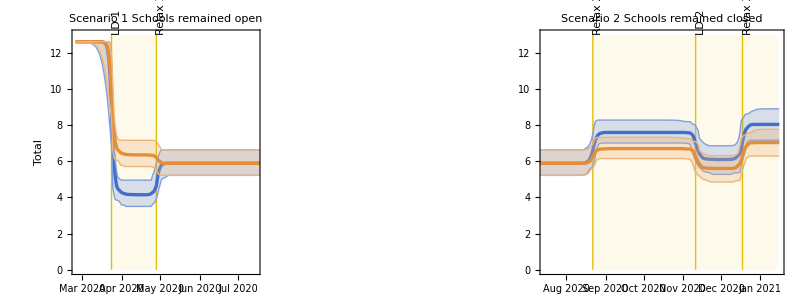
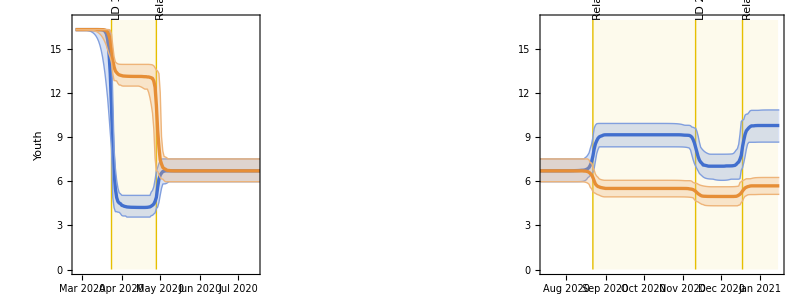
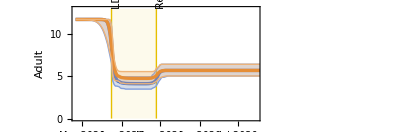
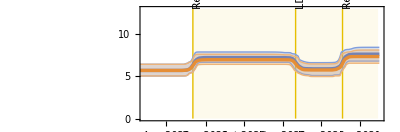
-Graphics-
-Graphics-
-Graphics- | -Graphics-                           Average contacts (1/day)

```mathematica
(* Plotting *)
aveContsTotal2Plot = {averageContactsTotal[[1,All,All]],
averageContactsTotal[[2,All,All]],
averageContactsTotal[[3,All,All]]};
aveContsYouth2Plot  ={averageContactsYouth[[1,All,All]],
averageContactsYouth[[2,All,All]],
averageContactsYouth[[3,All,All]]};
aveContsAdults2Plot ={averageContactsAdults[[1,All,All]],
averageContactsAdults[[2,All,All]],
averageContactsAdults[[3,All,All]]};

figContsTotal= plotScenarioTrajectories[aveContsTotal2Plot,"Total",{"Scenario 1\nSchools remained open","Scenario 2\nSchools remained closed"},{ticksInvisible,ticksInvisible},{{0,13},{0,13}},{"a", "b"}, "righter",Graphics[], {{},{},{}}, False,True,0.33,400];
figContsYouth= plotScenarioTrajectories[aveContsYouth2Plot,"Youth",{"",""},{ticksInvisible,ticksInvisible},{{0,17},{0,17}}, {"c", "d"}, "righter",Graphics[], {{},{},{}}, False,True,0.33,400];
figContsAdults= plotScenarioTrajectories[aveContsAdults2Plot,"Adult",{"",""},{ticksVisible,ticksVisible},{{0,13},{0,13}}, {"e", "f"}, "righter",Graphics[], {{},{},{}}, False,"elas",0.33,400];

figContsTotalAges = Labeled[Grid[{{figContsTotal},{figContsYouth}, {figContsAdults}}],Style[Rotate["                           Average contacts (1/day)",Pi/2],Black,FontSize->sizeFontBig,FontFamily->"Helvetica",TextAlignment->Center,Background->None],Left];
exportFigs[figContsTotalAges, "SFig3"];
```

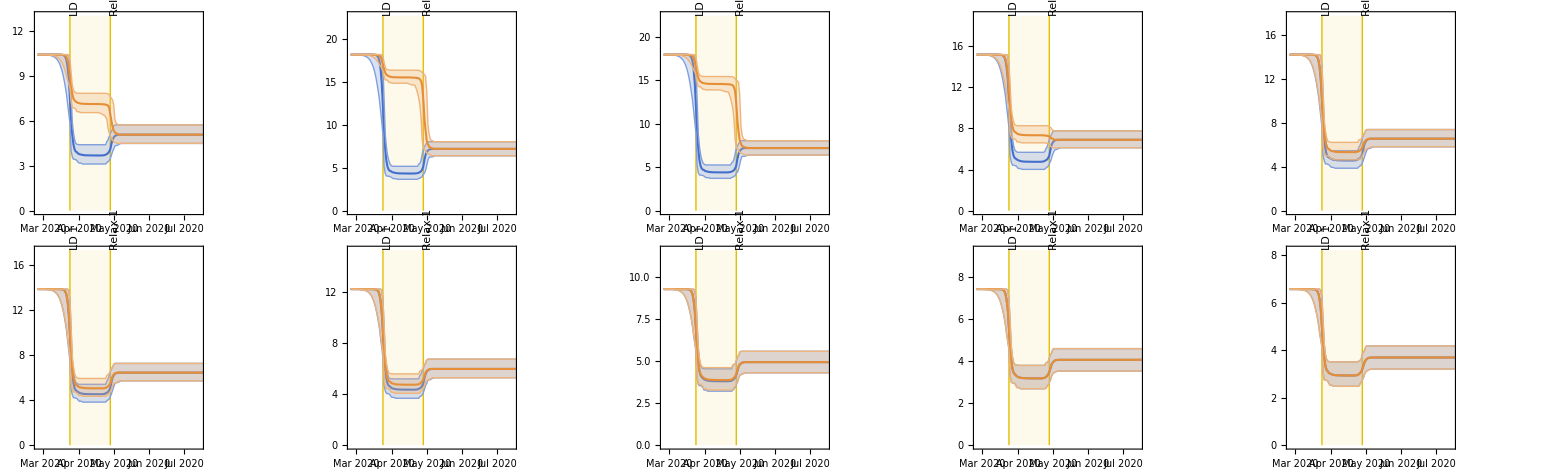
| Scenario 1
Schools remained open
Average contacts (1/day) | -Graphics-
 |

```mathematica
indivAverageContacts = Total[contactMatricesScenarios, {5}];

figContacts10Scen1=Table[
Module[{maxVal, maxRange}, 
maxVal = Quantile[indivAverageContacts[[2, All, All, k]], 0.975];
maxRange = Max[maxVal] + Max[maxVal]/4;
plotWithLetter[{plotLineWithCrI[indivAverageContacts[[1, All, All, k]],colorBlue,"","","",1,If[k>=6,ticksVisible, ticksInvisible],{0, maxRange}, 0.75, 250],
plotLineWithCrI[indivAverageContacts[[2, All, All, k]],colorOrange]},ageLabelShort[[k]],Scaled[{0.85,0.9}], sizeFontBig, Black]], {k, 1, numAgeGroups}];

figContacts10Scen1 = Grid[{{"", Style["Scenario 1\nSchools remained open",TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{Style[Rotate["Average contacts (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figContacts10Scen1, {2,5}]]},
{"", legendRawScen1ElasFlat}}];
exportFigs[figContacts10Scen1, "SFig4"];
```

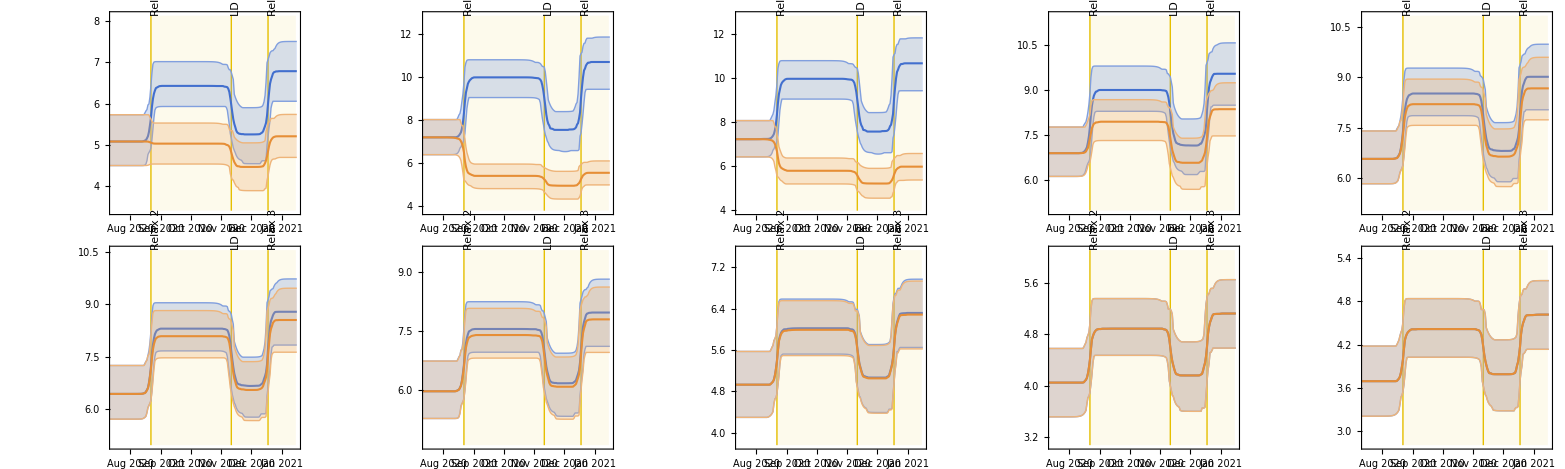
| Scenario 2
Schools remained closed
Average contacts (1/day) | -Graphics-
 |

```mathematica
figContacts10Scen2=Table[Module[{maxVal,minVal,minRange,maxRange},maxVal=Quantile[indivAverageContacts[[1,All,Range[150,300],k]],0.975];
minVal=Quantile[indivAverageContacts[[3,All,Range[150,300],k]],0.025];
maxRange=Max[maxVal]+Max[maxVal]/8;
minRange=Min[minVal]-Min[minVal]/8;
plotWithLetter[{plotLineWithCrI[indivAverageContacts[[1,All,All,k]],colorBlue,"","","",2,If[k>=6,ticksVisible,ticksInvisible],{minRange,maxRange},0.75,250],plotLineWithCrI[indivAverageContacts[[3,All,All,k]],colorOrange]},ageLabelShort[[k]],Scaled[{0.45,0.9}],sizeFontBig,Black]],{k,1,numAgeGroups}];

figContacts10Scen2 = Grid[{{"", Style["Scenario 2\nSchools remained closed",TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{Style[Rotate["Average contacts (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figContacts10Scen2, {2,5}]]},
{"", legendRawScen2ElasFlat}}];
exportFigs[figContacts10Scen2, "SFig5"];
```

### Estimated parameters

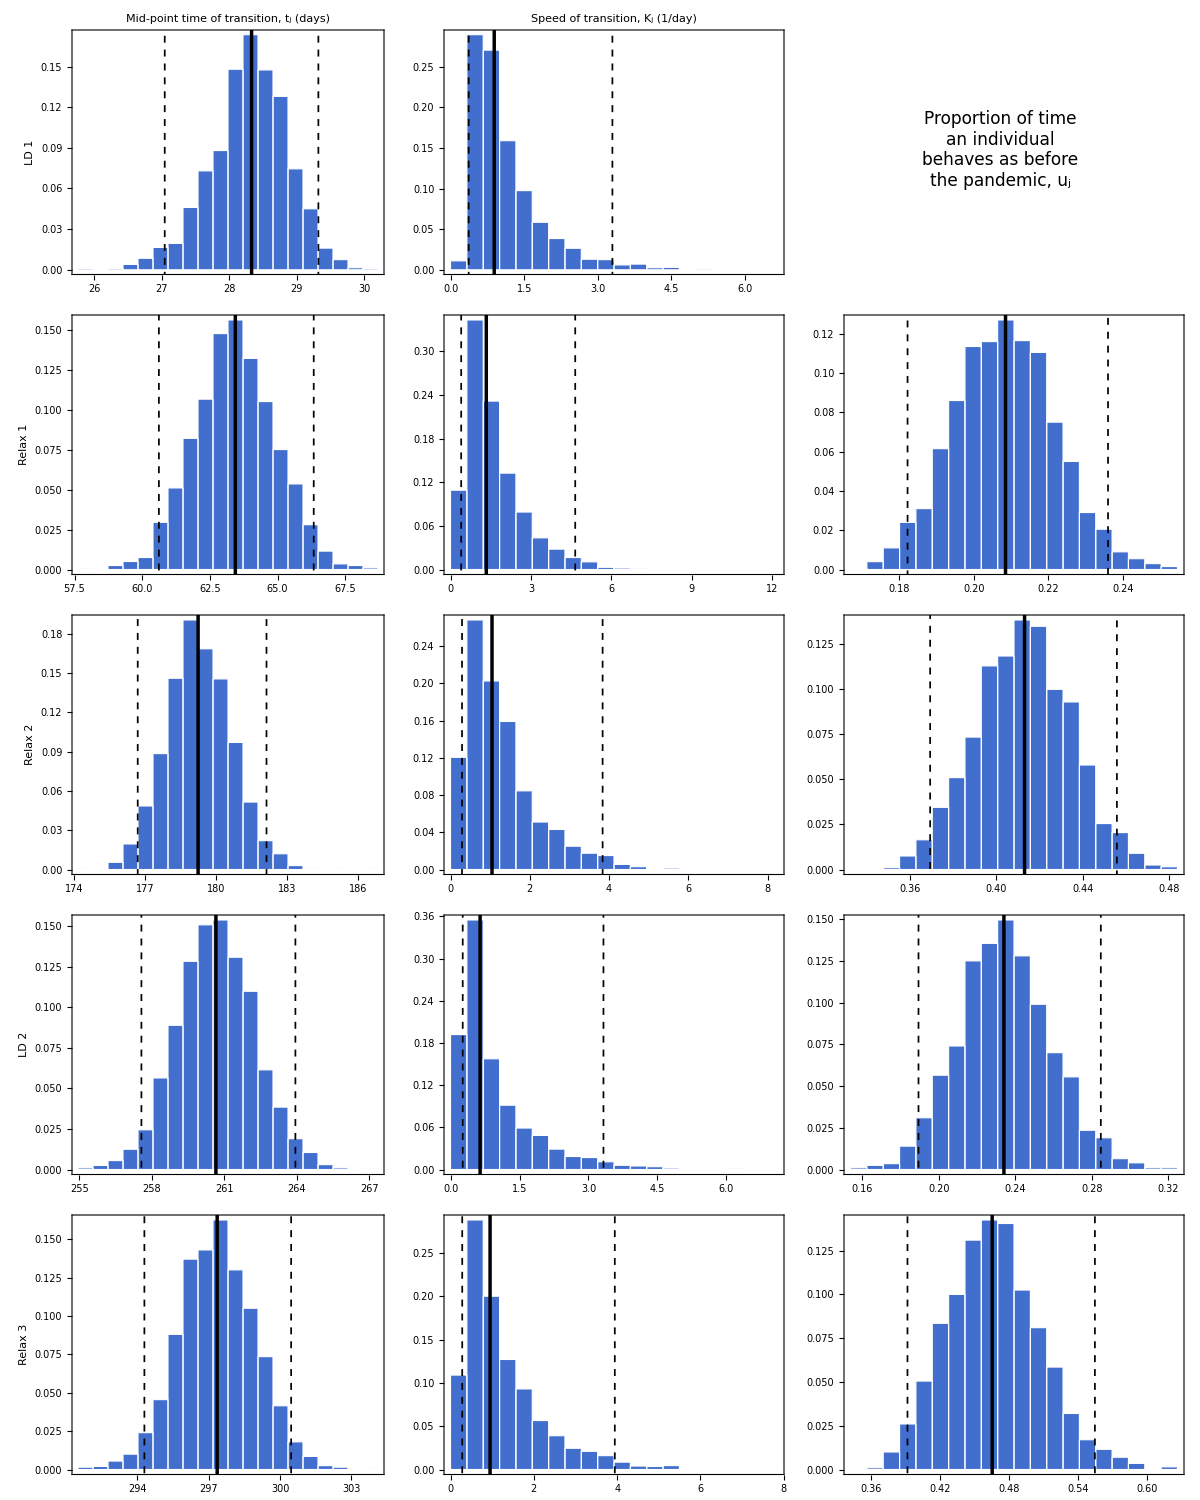

```mathematica
(* Plotting contact-related parameters *)

parameterTVals = {estimatesData⟦All,20⟧,estimatesData⟦All,22⟧,estimatesData⟦All,24⟧,estimatesData⟦All,26⟧,estimatesData⟦All,28⟧};
parameterKVals = {estimatesData⟦All,21⟧,estimatesData⟦All,23⟧,estimatesData⟦All,25⟧,estimatesData⟦All,27⟧,estimatesData⟦All,29⟧};
parameterUVals = {estimatesData⟦All,30⟧,estimatesData⟦All,31⟧,estimatesData⟦All,32⟧,estimatesData⟦All,33⟧};

figT = Table[plotWithLetter[plotHistogram[parameterTVals[[i]], If[i == 1, Style["Mid-point time of transition, \nt_j (days)"], ""],
"", Style[transitionDatesLabelsShort[[i]]], colorBlue], parameterTXLabel[[i]], "right", sizeFontBig],{i, 1, Length[parameterTVals]}];
figK = Table[plotWithLetter[
{plotHistogram[parameterKVals[[i]], If[i == 1, Style["Speed of transition, \nK_j (1/day)"], ""],"",  "", colorBlue]}, parameterKXLabel[[i]], "right", sizeFontBig],{i, 1, Length[parameterKVals]}];
figU = Table[plotWithLetter[
{plotHistogram[parameterUVals[[i]], "", "",  "", colorBlue,
If[i == 2, {0.33, 0.49},True]]}, parameterUXLabel[[i]], "right", sizeFontBig],{i, 1, Length[parameterUVals]}];
figU = Prepend[figU,Graphics[Text[Style["Proportion of time\nan individual\nbehaves as before\nthe pandemic, u_j\n\n\n\n", sizeFontBig]]]];

figContParams = Grid[Transpose[{figT, figK, figU}]];
exportFigs[figContParams, "SFig6"];
```

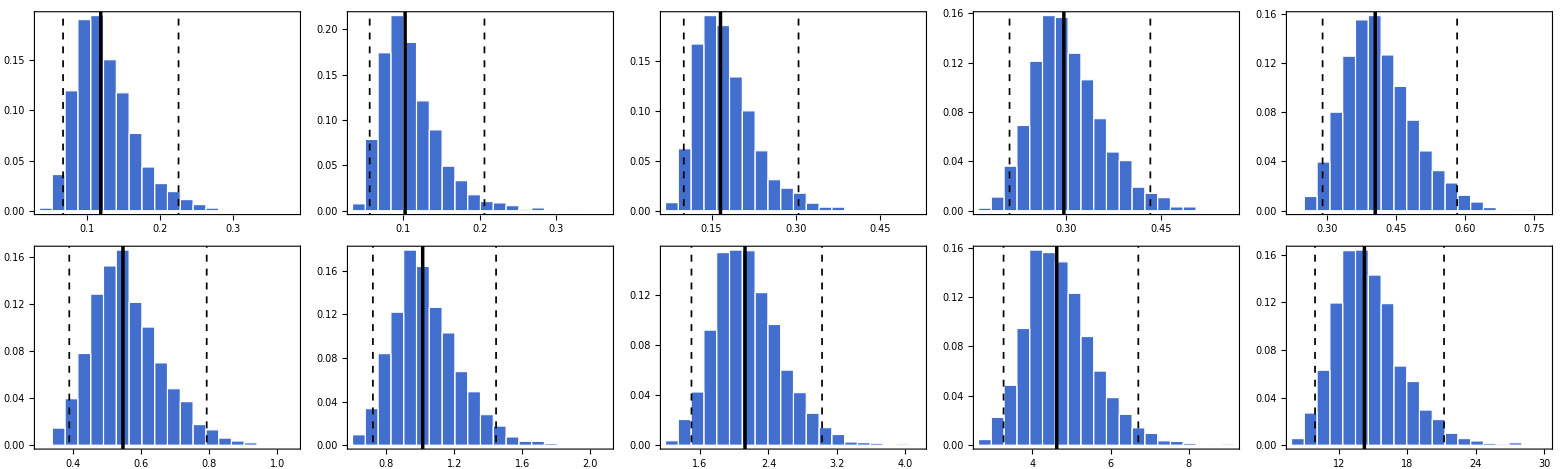
| Hospitalization rates, ν_k (1/day)
Probability | -Graphics-

```mathematica
(* Plotting hospitalization rates *)
parameterHospRateVals = Table[365 estimatesData⟦All,2+i⟧,{i,1,numAgeGroups}];

figHospRates = Table[plotWithLetter[
{plotHistogram[parameterHospRateVals[[i]], "","",  "", colorBlue,
Which[i == 1,{0.04, 0.27},i == 2,{0.02, 0.29},True, True]]}, ageLabelShort[[i]], Scaled[{0.85, 0.9}], sizeFontBig, Black],{i, 1, Length[parameterHospRateVals]}];

figHospRates = Grid[{{"", Style[Rotate["Hospitalization rates, ν_k (1/day)",0],Black,sizeFontBig, FontFamily->"Helvetica"]},{Style[Rotate["Probability",Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"], Grid[ArrayReshape[figHospRates, {2,5}]]}}];
exportFigs[figHospRates, "SFig7"];
```

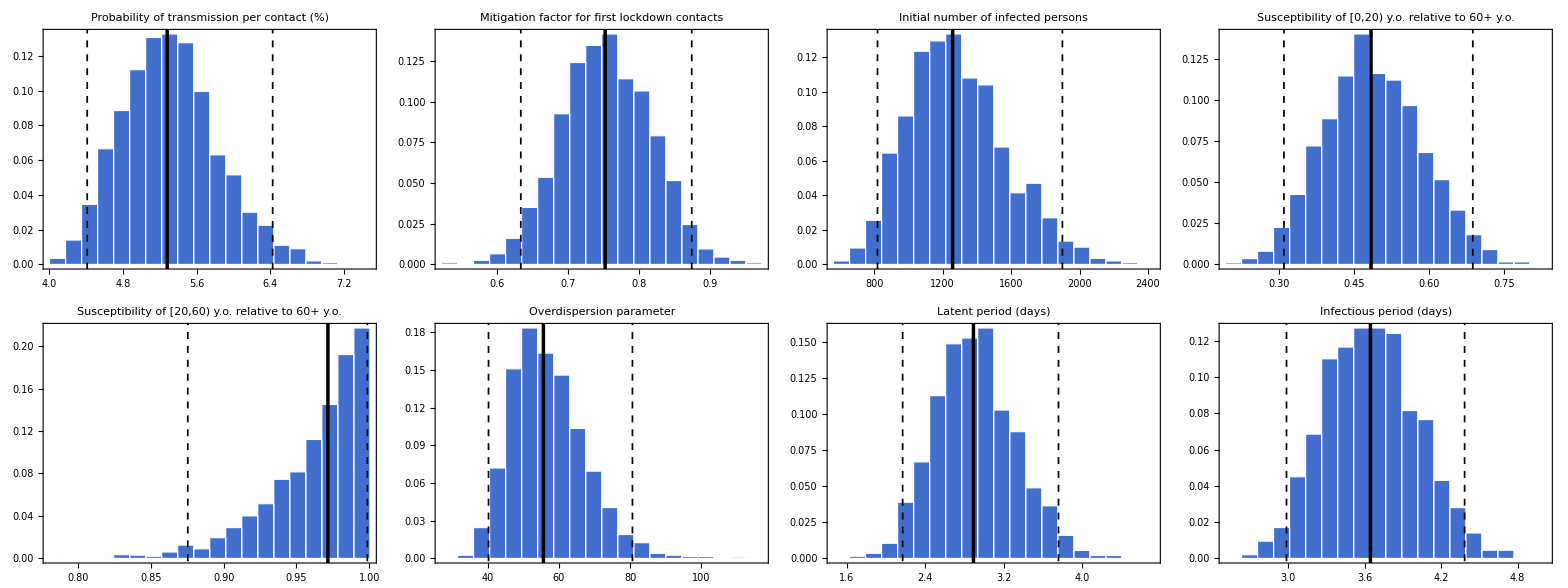
Probability | -Graphics-

```mathematica
(* Plotting all the other remaining parameters *)
parameterConstVals = {estimatesData⟦All,1⟧ 100,estimatesData⟦All,2⟧,estimatesData⟦All,13⟧ Total[demographyData10],estimatesData⟦All,14⟧,estimatesData⟦All,15⟧,estimatesData⟦All,17⟧,1/estimatesData⟦All,18⟧,1/estimatesData⟦All,19⟧};

figConstsTables = Table[plotWithLetter[plotHistogram[parameterConstVals[[i]], Style[parameterConstXLabel[[i]]],
"","", colorBlue], parameterConstXLabelShort[[i]], Which[i==2,Scaled[{1.0,0.9}],i==3, Scaled[{0.8, 0.9}], i == 5, Scaled[{0.2, 0.9}],True, "right"], sizeFontBig],{i, 1, Length[parameterConstVals]}];
(*figSRF = plotWithLetter[plotHistogram[1-schRedFacObtained, Style["\nSchool reduction factor"],
"", "", colorBlue],"1-ζ_s", "right", sizeFontBig];*)
figConstsParams = Grid[{{Style[Rotate["Probability",Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"], Grid[ArrayReshape[{figConstsTables}, {2,4}]]}}];

exportFigs[figConstsParams, "SFig8"];
```

```mathematica
allParametersEstimated = Join[parameterTVals, parameterKVals, parameterUVals, parameterConstVals, parameterHospRateVals];
allParametersEstimatedLabels = Join[Table[Subscript["t",k],{k,0,4}], parameterKXLabel,parameterUXLabel,parameterConstXLabelShort, Table[Subscript["ν",age],{age,ageLabelShort}]];

rawCorr=Correlation[Transpose[allParametersEstimated]];
n=Length[rawCorr];
maskedCorr=Table[If[row>col,rawCorr[[row,col]],-999],{row,1,n},{col,1,n}];

leftLabels=allParametersEstimatedLabels;
leftLabels[[1]]=""; 
topLabels=allParametersEstimatedLabels;
topLabels[[-1]]=""; 

leftLabelsFormatted=Transpose[{Range[n],allParametersEstimatedLabels}];
topLabelsTilted=Transpose[{Range[n],Rotate[#,Pi/2]&/@allParametersEstimatedLabels}];

leftLabelsFormatted=Rest[leftLabelsFormatted];
topLabelsTilted=Most[topLabelsTilted];

legendColor=ColorData["LightTemperatureMap"][Rescale[#,{-1,1},{0,1}]]&;
customColor[val_]:=If[val==-999,White,legendColor[val]];

figMaskedCorr = MatrixPlot[maskedCorr,ColorFunction->customColor,ColorFunctionScaling->False,PlotLegends->BarLegend[{legendColor,{-1,1}},LegendLabel->"Correlation"],PlotRangePadding->None,DataReversed->{True,False},Frame->True,FrameStyle->White,FrameTicksStyle->Directive[Black,FontSize->12],FrameTicks->{{leftLabelsFormatted,None},{None,topLabelsTilted}},GridLines->None,Mesh->None,ImageSize->750];

exportFigs[figMaskedCorr, "SFig9"];
```

-Graphics-

### Model fit to seroprevalence data

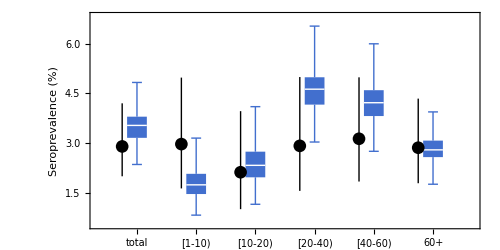

```mathematica
(* Plotting *)
seroEstimatesMay28 = {seroprevalenceScenariosTotal[[1,1,All,93]],seroprevalenceScenariosRegrouped[[1, 1, All, 93]], seroprevalenceScenariosRegrouped[[1, 2, All, 93]], seroprevalenceScenariosRegrouped[[1, 3, All, 93]], seroprevalenceScenariosRegrouped[[1, 4, All, 93]], seroprevalenceScenariosRegrouped[[1, 5, All, 93]]};

figSeroDataEstimate = Legended[Show[{plotBoxWhisker[seroEstimatesMay28, {colorBlue}, {"total", "[1-10)", "[10-20)", "[20-40)", "[40-60)", "60+"},
"", "Seroprevalence (%)"],
ListPlot[Transpose[{Range[6]-0.25,seroDataMay28Around}], PlotMarkers->{Automatic, 13},PlotStyle -> Black, IntervalMarkers -> "Fences", IntervalMarkersStyle -> {Black, Thick}]}],
Placed[Row[{
Column[{
PointLegend[{None},{Style["Data",FontSize->sizeFontSmall]},LegendMarkers->{{Graphics[{Black,Style[Disk[]]}]}},LegendMarkerSize->10],
PointLegend[{None},{Style["Model",FontSize->sizeFontSmall]},LegendMarkers->{{Graphics[{colorBlue,Style[Rectangle[], EdgeForm[White]]}]}},LegendMarkerSize->12]}]
}], {Left, Top}]];
exportFigs[figSeroDataEstimate, "SFig10"];
```

### Model fit to hospitalization data

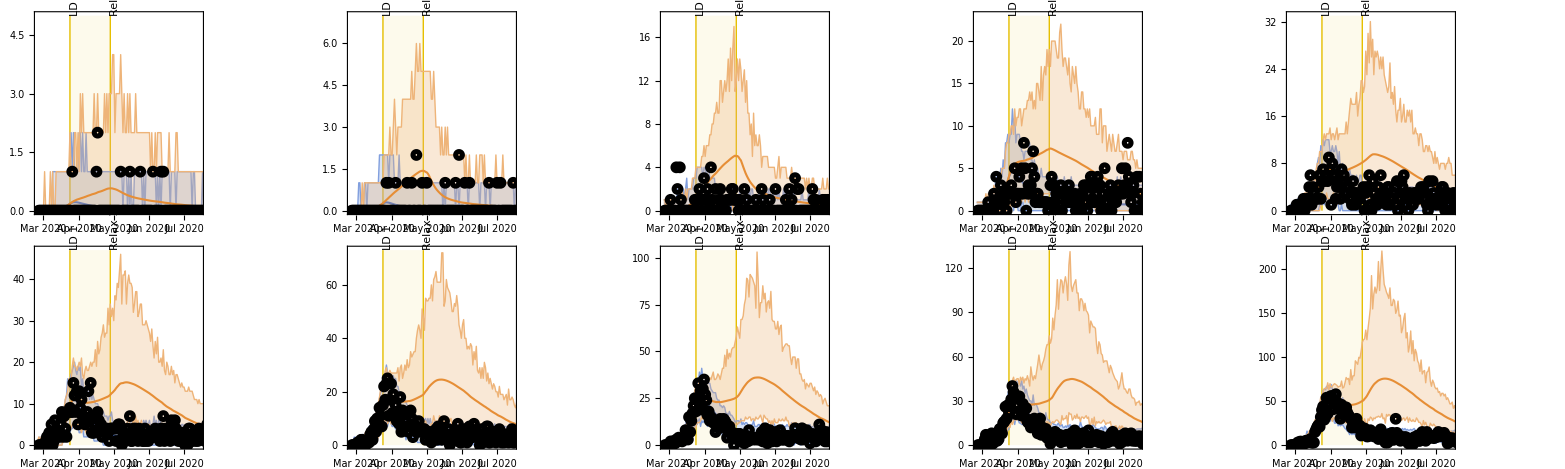
| Scenario 1
Schools remained open
Hospitalizations (1/day) | -Graphics-
 |

```mathematica
scatterPlotHospData10Groups[k_] := DateListPlot[hospitalizationData[[All,k]], "February 26, 2020", Joined->False, PlotTheme -> "Web",PlotMarkers->{Graphics[{Black,Style[Circle[],Thickness[0.25]]}],5}];

figHosp10Scen1=Table[
Module[{maxVal, maxRange}, 
maxVal = Quantile[hospitalizationSimulatedScenarios[[2, k, All, All]], 0.975];
maxRange = Max[maxVal]+1;
plotWithLetter[{plotLineWithCrI[hospitalizationSimulatedScenarios[[1, k, All, All]],colorBlue,"","","",1,If[k>=6,ticksVisible, ticksInvisible],{0, maxRange}, 0.75, 250, Solid, hospitalizationScenarios[[1,k,All,All]]],
plotLineWithCrI[hospitalizationSimulatedScenarios[[2, k, All, All]],colorOrange,"","","",1,If[k>=6,ticksVisible, ticksInvisible],{0, maxRange}, 0.75, 250, Solid, hospitalizationScenarios[[2,k,All,All]]],
scatterPlotHospData10Groups[k]},ageLabelShort[[k]],Scaled[{0.85,0.9}], sizeFontBig, Black]], {k, 1, numAgeGroups}];

figHosp10Scen1 = Grid[{{"", Style["Scenario 1\nSchools remained open",TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{Style[Rotate["Hospitalizations (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figHosp10Scen1, {2,5}]]},
{"", legendRawScen1HospFlat}}];
exportFigs[figHosp10Scen1, "SFig11"];
```

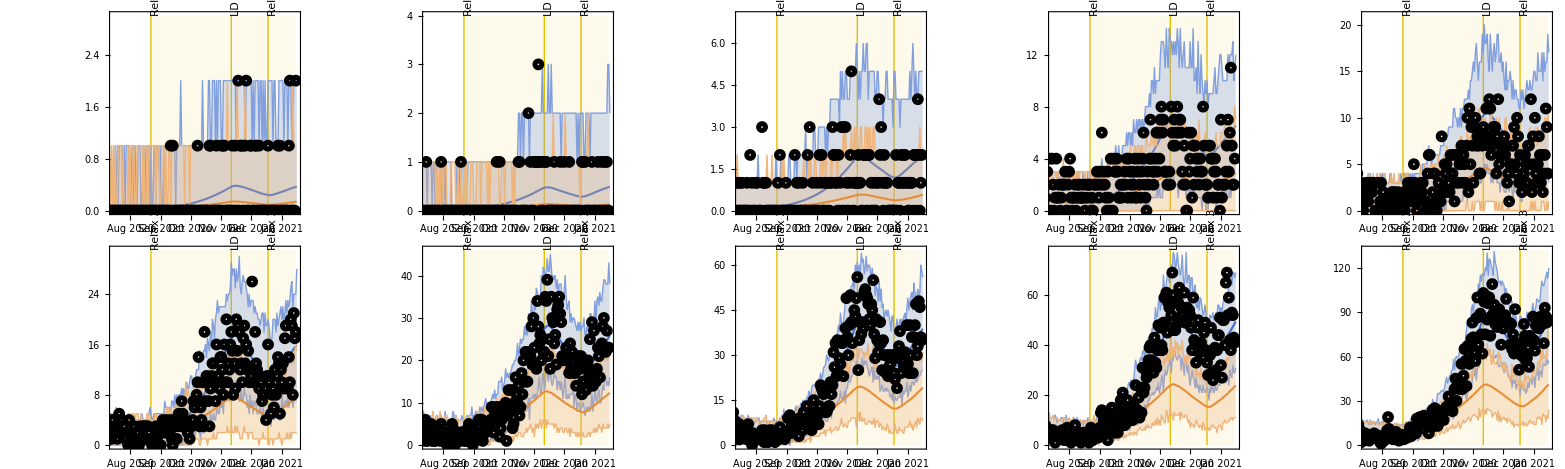
| Scenario 2
Schools remained closed
Hospitalizations (1/day) | -Graphics-
 |

```mathematica
figHosp10Scen2=Table[
Module[{maxVal, maxRange}, 
maxVal = Quantile[hospitalizationSimulatedScenarios[[1, k, All, All]], 0.975];
maxRange = Max[maxVal]+1;
plotWithLetter[{plotLineWithCrI[hospitalizationSimulatedScenarios[[1, k, All, All]],colorBlue,"","","",2,If[k>=6,ticksVisible, ticksInvisible],{0, maxRange}, 0.75,250, Solid, hospitalizationScenarios[[1,k,All,All]]],
plotLineWithCrI[hospitalizationSimulatedScenarios[[3, k, All, All]],colorOrange,"","","",2,If[k>=6,ticksVisible, ticksInvisible],{0, maxRange}, 0.75,250, Solid, hospitalizationScenarios[[3,k,All,All]]],
scatterPlotHospData10Groups[k]},ageLabelShort[[k]],Scaled[{0.45,0.9}], sizeFontBig, Black]], {k, 1, numAgeGroups}];

figHosp10Scen2 = Grid[{{"", Style["Scenario 2\nSchools remained closed",TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{Style[Rotate["Hospitalizations (1/day)", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figHosp10Scen2, {2,5}]]},{"", legendRawScen2HospFlat}}];
exportFigs[figHosp10Scen2, "SFig12"];
```

```mathematica
hospSimulCumu = Transpose[Accumulate[Transpose[Total[hospitalizationSimulatedScenarios, {2}],{2,3,1} ]], {3,1,2}];
hospCumu = Transpose[Accumulate[Transpose[Total[hospitalizationScenarios, {2}],{2,3,1} ]], {3,1,2}];
(*Print[Median[hospCumu[[1,All,93]]]]
Print[Quantile[hospSimulCumu[[1,All,93]],0.025]]
Print[Quantile[hospSimulCumu[[1,All,93]],0.975]]*)
```

### Age-specific contributions to R(t)

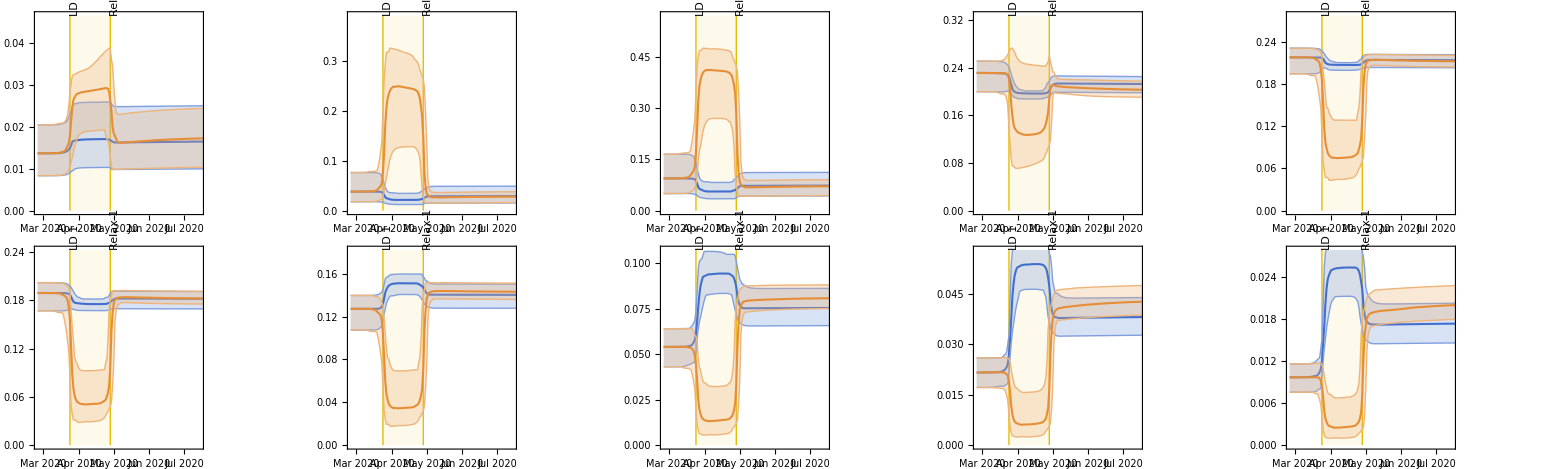
| Scenario 1
Schools remained open
Cumulative elasticities | -Graphics-
 |

```mathematica
figCumuElas10Scen1=Table[
Module[{maxVal, maxRange}, 
maxVal = Quantile[cumuElasScenarios[[2, All, All, k]], 0.975];
maxRange = Max[maxVal]+Max[maxVal]/5;
plotWithLetter[{plotLineWithCrI[cumuElasScenarios[[1, All, All, k]],colorBlue,"","","",1,If[k>=6,ticksVisible, ticksInvisible],{0, maxRange}, 0.75, 250],
plotLineWithCrI[cumuElasScenarios[[2, All, All, k]],colorOrange]},ageLabelShort[[k]],Scaled[{0.85,0.9}], sizeFontBig,Black]], {k, 1, numAgeGroups}];

figCumuElas10Scen1 = Grid[{{"", Style["Scenario 1\nSchools remained open",TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{Style[Rotate["Cumulative elasticities", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figCumuElas10Scen1, {2,5}]]},
{"", legendRawScen1ElasFlat}}];
exportFigs[figCumuElas10Scen1, "SFig13"];
```

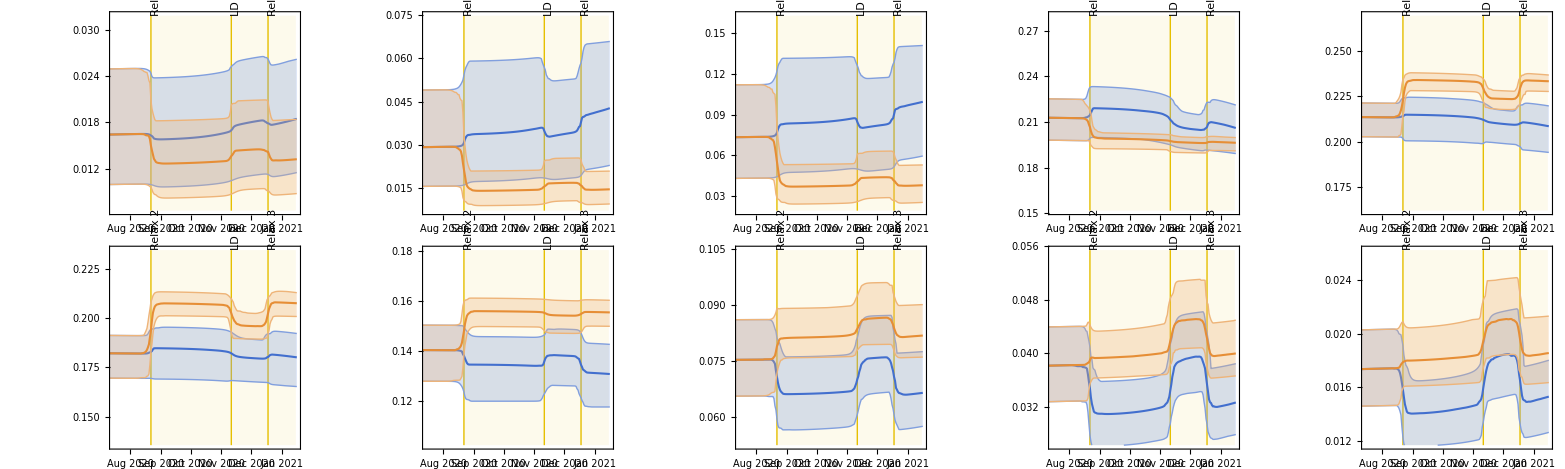
| Scenario 2
Schools remained closed
Cumulative elasticities | -Graphics-
 |

```mathematica
figCumuElas10Scen2=Table[
Module[{maxVal,minVal,minRange, maxRange}, 
maxVal = Quantile[cumuElasScenarios[[1,All, Range[150,300], k]], 0.975];
minVal = Quantile[Re[cumuElasScenarios[[3, All,Range[150,300], k]]], 0.025];
maxRange = Min[1,Max[maxVal]+Max[maxVal]/5];
minRange = Max[0,Min[minVal]-Min[minVal]/5];
plotWithLetter[{plotLineWithCrI[cumuElasScenarios[[1, All, All, k]],colorBlue,"","","",2,If[k>=6,ticksVisible, ticksInvisible],{minRange, maxRange},0.75, 250],
plotLineWithCrI[cumuElasScenarios[[3, All, All, k]],colorOrange]},ageLabelShort[[k]],Scaled[{0.45, 0.9}], sizeFontBig,Black]], {k, 1, numAgeGroups}];

figCumuElas10Scen2 = Grid[{{"", Style["Scenario 2\nSchools remained closed",TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{Style[Rotate["Cumulative elasticities", Pi/2],Black,sizeFontBig, FontFamily->"Helvetica"],Grid[ArrayReshape[figCumuElas10Scen2, {2,5}]]},
{"",legendRawScen2ElasFlat}}];
exportFigs[figCumuElas10Scen2, "SFig14"];
```

### Comparison of cumulative hospitalizations

```mathematica
hospMatrices = {hospitalizationScenarios,hospitalizationScenariosGrouped,hospitalizationScenariosTotal,hospitalizationSimulatedScenarios, hospitalizationSimulatedScenariosGrouped, hospitalizationSimulatedScenariosTotal};

cumuHospFunc[matrix_] := Table[Accumulate[matrix[[ii,jj,kk]]],
{ii, 1,Dimensions[matrix][[1]]},
{jj, 1, Dimensions[matrix][[2]]},
{kk, 1, Dimensions[matrix][[3]]}];
cumuHospMatrices= Table[cumuHospFunc[hospMatrices[[qq]]], {qq, 1, 6}];
cumuHospMatricesSelectDates= Table[N[cumuHospMatrices[[qq, All, All, All, {141, 325}]]], {qq, 1, 6}];
cumuHospMatricesSelectDatesEach = Map[Map[ReplacePart[#,{2}->#[[2]]-#[[1]]]&,#,{3}]&,cumuHospMatricesSelectDates];

stats4AgesHosp = getStats4Hosp[cumuHospMatricesSelectDatesEach[[1]], cumuHospMatricesSelectDatesEach[[4]]];
stats4GroupedHosp = getStats4Hosp[cumuHospMatricesSelectDatesEach[[2]], cumuHospMatricesSelectDatesEach[[5]]];
stats4TotalHosp = getStats4Hosp[cumuHospMatricesSelectDatesEach[[3]], cumuHospMatricesSelectDatesEach[[6]]];

relChange4AgesHospScen1 = getRelChange4Hosp[cumuHospMatricesSelectDatesEach[[1]], cumuHospMatricesSelectDatesEach[[4]],1];
relChange4GroupedHospScen1 = getRelChange4Hosp[cumuHospMatricesSelectDatesEach[[2]], cumuHospMatricesSelectDatesEach[[5]],1];
relChange4TotalHospScen1 = getRelChange4Hosp[cumuHospMatricesSelectDatesEach[[3]], cumuHospMatricesSelectDatesEach[[6]],1];
relChange4AgesHospScen2 = getRelChange4Hosp[cumuHospMatricesSelectDatesEach[[1]], cumuHospMatricesSelectDatesEach[[4]],2];
relChange4GroupedHospScen2 = getRelChange4Hosp[cumuHospMatricesSelectDatesEach[[2]], cumuHospMatricesSelectDatesEach[[5]],2];
relChange4TotalHospScen2 = getRelChange4Hosp[cumuHospMatricesSelectDatesEach[[3]], cumuHospMatricesSelectDatesEach[[6]],2];
```

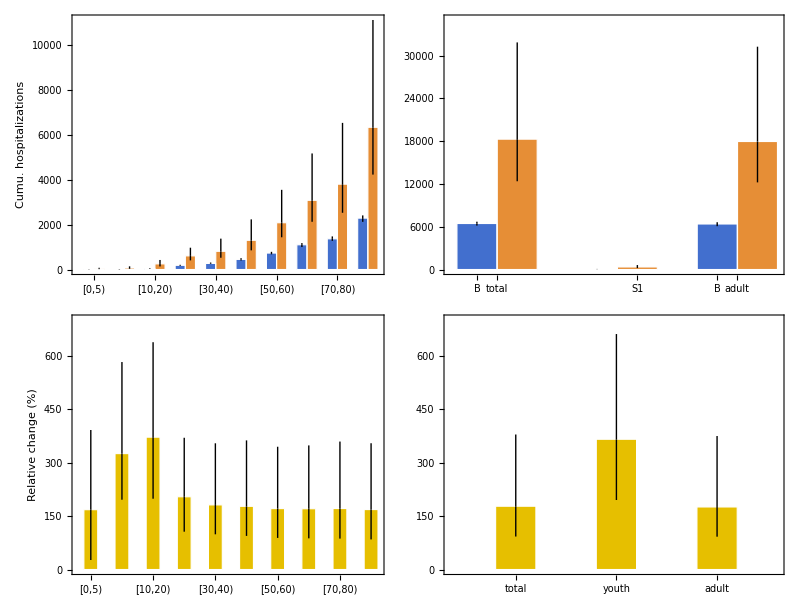

```mathematica
hospAbsScen1TotalGrouped = {{transformToAround[Ceiling[stats4TotalHosp[[All,1,1,1]]],0],
transformToAround[Ceiling[stats4TotalHosp[[All,2,1,1]]],0]},
{transformToAround[Ceiling[stats4GroupedHosp[[All,1,1,1]]],0],
transformToAround[Ceiling[stats4GroupedHosp[[All,2,1,1]]],0]},
{transformToAround[Ceiling[stats4GroupedHosp[[All,1,2,1]]],0],
transformToAround[Ceiling[stats4GroupedHosp[[All,2,2,1]]],0]}};
hospAbsScen1Ages = Transpose[Outer[transformToAround[Ceiling[stats4AgesHosp[[All,#1,#2,1]]], 0]&,{1,2},Range[1,10]]];


figHospScen1BarsAbsAges = Legended[
plotWithLetter[
{plotBarWithError[hospAbsScen1Ages, {colorBlue, colorOrange}, {ageLabelShort, None}, "", "Cumu. hospitalizations", "", {0,Automatic}, 550, 150/550],
Graphics[{Inset[plotBarWithError[hospAbsScen1Ages[[1;;3]], {colorBlue, colorOrange}, {ageLabelShort, None}, "", "", "", {0,500}],
Scaled[{0.15, 0.45}], {Center, Center}, Scaled[0.875]]}]}, "a", "lefter"],
Placed[Row[{
Column[{
PointLegend[{None},{Style["Baseline",FontSize->sizeFontSmall]},LegendMarkers->{{Graphics[{colorBlue,Style[Rectangle[], EdgeForm[White]]}]}},LegendMarkerSize->12],
PointLegend[{None},{Style["Scenario 1",FontSize->sizeFontSmall]},LegendMarkers->{{Graphics[{colorOrange,Style[Rectangle[], EdgeForm[White]]}]}},LegendMarkerSize->12]}]
}]
,{Center, Top}]];

figHospScen1BarsAbsTot=plotWithLetter[
{plotBarWithError[hospAbsScen1TotalGrouped, {colorBlue, colorOrange}, {{"total", "youth", "adult"}, {"B", "S1"}}, "", "", "", {0,35000}, 400, 150/400],
Graphics[{Inset[plotBarWithError[hospAbsScen1TotalGrouped[[2]], {colorBlue, colorOrange}, {{"youth"}}, "", "", "", {0,650}, 400, 250/400, {0.01, 1}, {0,3}],
Scaled[{0.5, 0.55}], {Center, Center}, Scaled[0.95]]}]},
"b", "lefter"];

figHospScen1BarsRelAges = plotWithLetter[
plotBarWithError[relChange4AgesHospScen1, colorYellowBright, ageLabelShort, "", "Relative change (%)", "", {0,700},550, 150/550, 1.25], "c", "lefter"];

figHospScen1BarsRelTot= plotWithLetter[
plotBarWithError[
Flatten[{relChange4TotalHospScen1, relChange4GroupedHospScen1[[1]], relChange4GroupedHospScen1[[2]]}],
colorYellowBright, {"total", "youth", "adult"}, "", "", "", {0,700},400, 150/400, 1.5],
"d", "lefter"];

figHospScen1Bars= Grid[{{figHospScen1BarsAbsAges,figHospScen1BarsAbsTot},
{figHospScen1BarsRelAges,figHospScen1BarsRelTot}}];
exportFigs[figHospScen1Bars, "SFig15"];
```

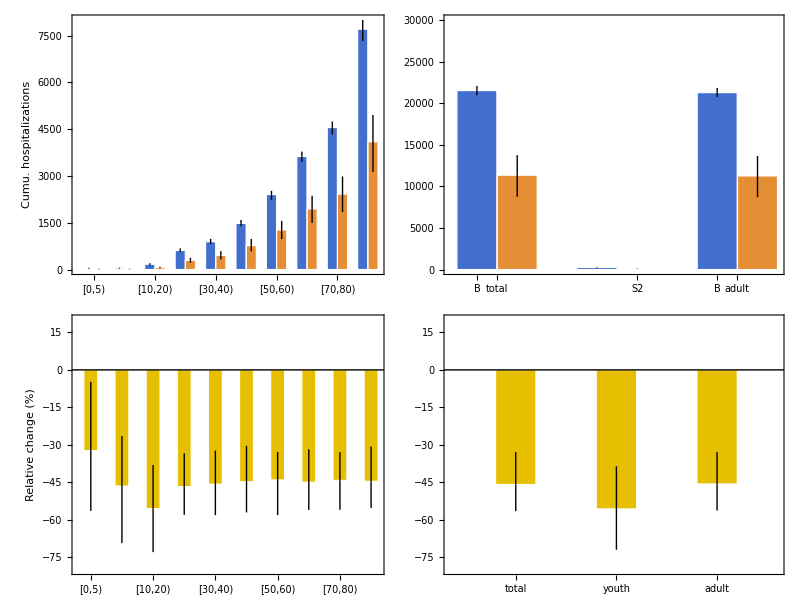

```mathematica
hospAbsScen2TotalGrouped = {{transformToAround[Ceiling[stats4TotalHosp[[All,1,1,2]]],0],
transformToAround[Ceiling[stats4TotalHosp[[All,3,1,2]]],0]},
{transformToAround[Ceiling[stats4GroupedHosp[[All,1,1,2]]],0],
transformToAround[Ceiling[stats4GroupedHosp[[All,3,1,2]]],0]},
{transformToAround[Ceiling[stats4GroupedHosp[[All,1,2,2]]],0],
transformToAround[Ceiling[stats4GroupedHosp[[All,3,2,2]]],0]}};
hospAbsScen2Ages = Transpose[Outer[transformToAround[Ceiling[stats4AgesHosp[[All,#1,#2,2]]], 0]&,{1,3},Range[1,10]]];

figHospScen2BarsAbsAges = Legended[plotWithLetter[
{plotBarWithError[hospAbsScen2Ages, {colorBlue, colorOrange}, {ageLabelShort, None}, "", "Cumu. hospitalizations", "", {0,Automatic}, 550, 150/550],
Graphics[{Inset[plotBarWithError[hospAbsScen2Ages[[1;;3]], {colorBlue, colorOrange}, {ageLabelShort, None}, "", "", "", {0,200}],
Scaled[{0.15, 0.45}], {Center, Center}, Scaled[0.875]]}]}, "a", "lefter"],
Placed[Row[{
Column[{
PointLegend[{None},{Style["Baseline",FontSize->sizeFontSmall]},LegendMarkers->{{Graphics[{colorBlue,Style[Rectangle[], EdgeForm[White]]}]}},LegendMarkerSize->12],
PointLegend[{None},{Style["Scenario 2",FontSize->sizeFontSmall]},LegendMarkers->{{Graphics[{colorOrange,Style[Rectangle[], EdgeForm[White]]}]}},LegendMarkerSize->12]}]
}]
,{Center, Top}]];

figHospScen2BarsAbsTot=plotWithLetter[
{plotBarWithError[hospAbsScen2TotalGrouped, {colorBlue, colorOrange}, {{"total", "youth", "adult"}, {"B", "S2"}}, "", "", "", {0,30000}, 400, 150/400],
Graphics[{Inset[plotBarWithError[hospAbsScen2TotalGrouped[[2]], {colorBlue, colorOrange}, {{"youth"}}, "", "", "", {0,300}, 400, 250/400, {0.01, 1}, {0,3}],
Scaled[{0.5, 0.55}], {Center, Center}, Scaled[0.95]]}]},
"b", "lefter"];

figHospScen2BarsRelAges = plotWithLetter[
{plotBarWithError[relChange4AgesHospScen2, colorYellowBright, ageLabelShort, "", "Relative change (%)", "", {-80, 20},550, 150/550, 1.25],
Graphics[{Black,InfiniteLine[{1,0},{2,0}]}]}, "c", "lefter"];

figHospScen2BarsRelTot= plotWithLetter[
{plotBarWithError[
Flatten[{relChange4TotalHospScen2, relChange4GroupedHospScen2[[1]], relChange4GroupedHospScen2[[2]]}],
colorYellowBright, {"total", "youth", "adult"}, "", "", "", {-80, 20},400, 150/400, 1.5],
Graphics[{Black,InfiniteLine[{1,0},{2,0}]}]},
"d", "lefter"];

figHospScen2Bars= Grid[{{figHospScen2BarsAbsAges,figHospScen2BarsAbsTot},
{figHospScen2BarsRelAges,figHospScen2BarsRelTot}}];
exportFigs[figHospScen2Bars, "SFig16"];
```

### Model projections for seroprevalence

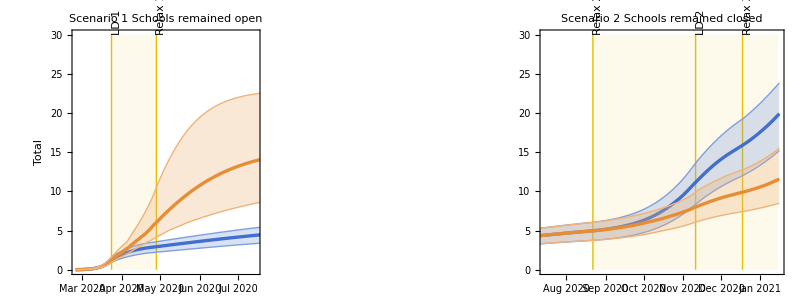
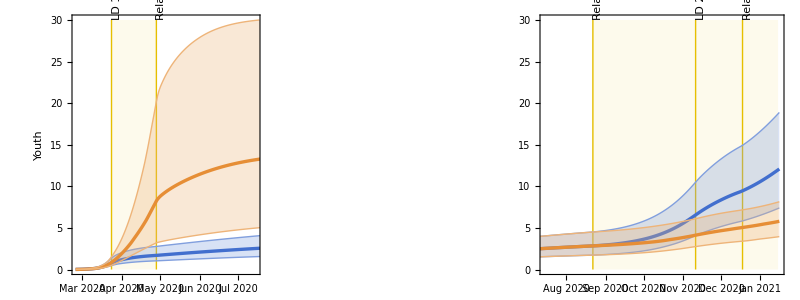
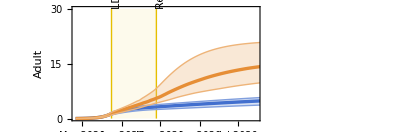
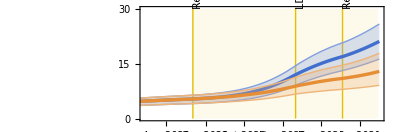
-Graphics-
-Graphics-
-Graphics- | -Graphics-                           Seroprevalences (%)

```mathematica
(* Plotting *)
(* We only have one data point on May 28 2020 *)scatterPlotSeroSinglePoint = DateListPlot[{Around[totalMeanSero, {Abs[totalMeanSero - totalLowMeanSero], Abs[totalHighMeanSero-totalMeanSero]}]}, AbsoluteTime["May 28, 2020"], PlotMarkers->{Automatic,10},PlotStyle -> {Black},IntervalMarkers->"Fences",IntervalMarkersStyle->{Black,Thick}, PlotStyle->"Web"];

seroTotal2Plot = {seroprevalenceScenariosTotal[[1,1, All, All]],
seroprevalenceScenariosTotal[[2,1, All, All]],
seroprevalenceScenariosTotal[[3,1, All, All]]};
seroYouth2Plot = {seroprevalenceScenariosGrouped[[1,1, All, All]],
seroprevalenceScenariosGrouped[[2,1, All, All]],
seroprevalenceScenariosGrouped[[3,1, All, All]]};
seroAdult2Plot = {seroprevalenceScenariosGrouped[[1,2, All, All]],
seroprevalenceScenariosGrouped[[2,2, All, All]],
seroprevalenceScenariosGrouped[[3,2, All, All]]};

figSeroTotal= plotScenarioTrajectories[seroTotal2Plot,"Total",{"Scenario 1\nSchools remained open","Scenario 2\nSchools remained closed"},{ticksInvisible,ticksInvisible},{{0,30},{0,30}},{"a", "b"}, "lefter", Graphics[], {{},{},{}},False,True,0.33,400];
figSeroChild= plotScenarioTrajectories[seroYouth2Plot,"Youth",{"",""},{ticksInvisible,ticksInvisible},{{0,30},{0,30}},{"c", "d"}, "lefter", Graphics[], {{},{},{}},False,True,0.33,400];
figSeroAdult= plotScenarioTrajectories[seroAdult2Plot,"Adult",{"",""},{ticksVisible,ticksVisible},{{0,30},{0,30}},{"e", "f"}, "lefter", Graphics[], {{},{},{}},False,"elas",0.33,400];

figSero = Labeled[Grid[{{figSeroTotal},{figSeroChild},{figSeroAdult}}],Style[Rotate["                           Seroprevalences (%)",Pi/2],Black,FontSize->sizeFontBig,FontFamily->"Helvetica",TextAlignment->Center,Background->None],Left];
exportFigs[figSero, "SFig17"];
```

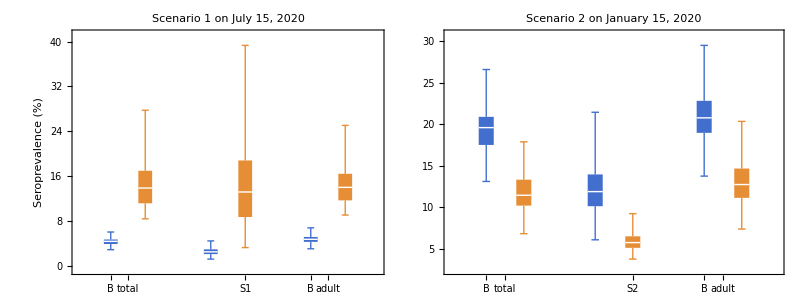

```mathematica
seroEstimates2PlotScen1 = {{seroprevalenceScenariosTotal[[1,1,All,141]],
seroprevalenceScenariosTotal[[2,1,All,141]]},
{seroprevalenceScenariosGrouped[[1,1,All,141]],
seroprevalenceScenariosGrouped[[2,1,All,141]]},
{seroprevalenceScenariosGrouped[[1,2,All,141]],seroprevalenceScenariosGrouped[[2,2,All,141]]}};
seroEstimates2PlotScen2 = {{seroprevalenceScenariosTotal[[1,1,All,325]],
seroprevalenceScenariosTotal[[3,1,All,325]]},
{seroprevalenceScenariosGrouped[[1,1,All,325]],
seroprevalenceScenariosGrouped[[3,1,All,325]]},
{seroprevalenceScenariosGrouped[[1,2,All,325]],seroprevalenceScenariosGrouped[[3,2,All,325]]}};
seroAroundScen1 = Map[getAround, seroEstimates2PlotScen1, {2}];
seroAroundScen2 = Map[getAround, seroEstimates2PlotScen2, {2}];

figSeroScen1BarChart = Legended[plotWithLetter[plotBoxWhisker[seroEstimates2PlotScen1, {colorBlue, colorOrange}, {{"total", "youth", "adult"}, {"B", "S1"}}, "", "Seroprevalence (%)", "Scenario 1 on July 15, 2020",1.5,0.33,500],"a", "lefter"],
Placed[Row[{
Column[{
PointLegend[{None},{Style["Baseline",FontSize->sizeFontSmall]},LegendMarkers->{{Graphics[{colorBlue,Style[Rectangle[], EdgeForm[White]]}]}},LegendMarkerSize->12],
PointLegend[{None},{Style["Scenario 1",FontSize->sizeFontSmall]},LegendMarkers->{{Graphics[{colorOrange,Style[Rectangle[], EdgeForm[White]]}]}},LegendMarkerSize->12]}]
}]
,{Right, Top}]];
figSeroScen2BarChart = Legended[plotWithLetter[
plotBoxWhisker[seroEstimates2PlotScen2, {colorBlue, colorOrange}, {{"total", "youth", "adult"}, {"B", "S2"}}, "", "", "Scenario 2 on January 15, 2020", 1.5,0.33,500], "b", "lefter"],
Placed[Row[{
Column[{
PointLegend[{None},{Style["Baseline",FontSize->sizeFontSmall]},LegendMarkers->{{Graphics[{colorBlue,Style[Rectangle[], EdgeForm[White]]}]}},LegendMarkerSize->12],
PointLegend[{None},{Style["Scenario 2",FontSize->sizeFontSmall]},LegendMarkers->{{Graphics[{colorOrange,Style[Rectangle[], EdgeForm[White]]}]}},LegendMarkerSize->12]}]
}]
,{Right,Top}]];

figSeroBarChart = Grid[{{figSeroScen1BarChart,figSeroScen2BarChart}}];
exportFigs[figSeroBarChart, "SFig18"];
```

### Uncertainty in the model projections

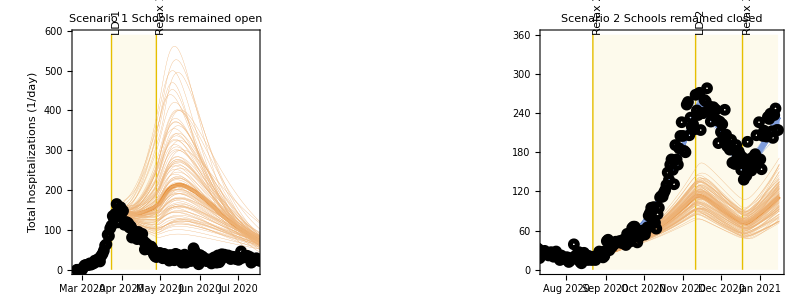
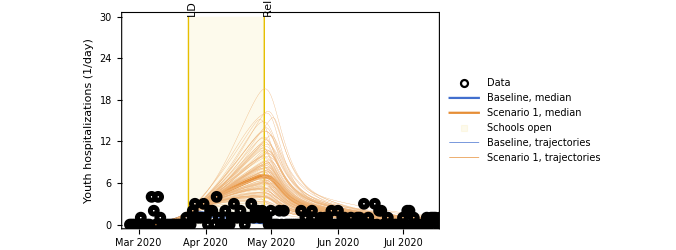
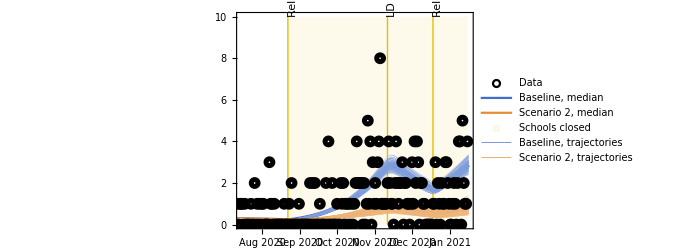
-Graphics-
-Graphics- | -Graphics-

```mathematica
figHospTotalSmooth = plotScenarioTrajectories[hospTot2Plot, "Total hospitalizations (1/day)",{"Scenario 1\nSchools remained open","Scenario 2\nSchools remained closed"},{ticksInvisible, ticksInvisible},{{0,590},{0,360}},{"a", "c"}, "lefter",scatterPlotHospData, 
hospTot2Plot, True];
figHospYouthSmooth = plotScenarioTrajectories[hospYouth2Plot, "Youth hospitalizations (1/day)",{"", ""},{ticksVisible, ticksVisible},{{0,30},{0,10}},{"b", "d"}, "lefter",scatterPlotHospDataChild, 
hospYouth2Plot, True, "indiv"];

figHospTotalYouthSmooth = Grid[{{figHospTotalSmooth}, {figHospYouthSmooth}}];
exportFigs[figHospTotalYouthSmooth, "SFig19"];
```

## Tables

```mathematica
timeIndex1 = 36; (*Apr 1 2020*)
timeIndex2 = 189;(*Sep 1 2020*)
timeEnd1= 141;
timeEnd2 = 325;
timeEnd2Adjusted = timeEnd2-30;
```

```mathematica
getAroundMedian[data_,data2_:Automatic]:=Module[{actualData2,numData1,numData2},
actualData2=If[data2===Automatic,data,data2];
numData1=If[MatchQ[data[[1]],_DateObject],AbsoluteTime/@data,data];
numData2=If[MatchQ[actualData2[[1]],_DateObject],AbsoluteTime/@actualData2,actualData2];
Around[Median[numData1],{Median[numData2]-Quantile[numData2,0.025],Quantile[numData2,0.975]-Median[numData2]}]];
```

```mathematica
hospMatrices = {hospitalizationScenariosGrouped,hospitalizationScenariosTotal, hospitalizationSimulatedScenariosGrouped, hospitalizationSimulatedScenariosTotal};
startDate=DateObject[{2020,2,25}];

getPeaks[singleDataMatrix_,scenarioLabel_String]:=
Module[{startDay,endDay,allPeakValues,allPeakIndices,allPeakDates},
Switch[scenarioLabel,
"Scenario 1",startDay=1;endDay=timeEnd1;,
"Scenario 2",startDay=timeEnd1+1;endDay=timeEnd2Adjusted;,
_,startDay=1;endDay=timeEnd2Adjusted;];

allPeakValues=Map[Max[#[[startDay;;endDay]]]&,singleDataMatrix,{-2}];
allPeakIndices=Map[Ordering[#[[startDay;;endDay]],-1][[1]]+startDay-1&,singleDataMatrix,{-2}];
allPeakDates=Map[DatePlus[startDate,#-1]&,allPeakIndices,{-1}];

{allPeakValues,allPeakDates}];

hospPeakResults1=getPeaks[#,"Scenario 1"]&/@hospMatrices;
hospPeakResults2=getPeaks[#,"Scenario 2"]&/@hospMatrices;
```

```mathematica
scen1Idx = {1,2};
scen2Idx = {1,3};

hospScen1PeakValTotal = Table[getAroundMedian[hospPeakResults1[[2]][[1,scen1Idx[[scenIdx]],1,All]],hospPeakResults1[[4]][[1,scen1Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen1Idx]}];
hospScen1PeakDateTotal = Table[getAroundMedian[hospPeakResults1[[2]][[2,scen1Idx[[scenIdx]],1,All]],hospPeakResults1[[4]][[2,scen1Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen1Idx]}];
hospScen1PeakValYouth =Table[getAroundMedian[hospPeakResults1[[1]][[1,scen1Idx[[scenIdx]],1,All]],hospPeakResults1[[3]][[1,scen1Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen1Idx]}];
hospScen1PeakDateYouth = Table[getAroundMedian[hospPeakResults1[[1]][[2,scen1Idx[[scenIdx]],1,All]],hospPeakResults1[[3]][[2,scen1Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen1Idx]}];
hospScen2PeakValTotal = Table[getAroundMedian[hospPeakResults2[[2]][[1,scen2Idx[[scenIdx]],1,All]],hospPeakResults2[[4]][[1,scen2Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen2Idx]}];
hospScen2PeakDateTotal = Table[getAroundMedian[hospPeakResults2[[2]][[2,scen2Idx[[scenIdx]],1,All]],hospPeakResults2[[4]][[2,scen2Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen2Idx]}];
hospScen2PeakValYouth = Table[getAroundMedian[hospPeakResults2[[1]][[1,scen2Idx[[scenIdx]],1,All]],hospPeakResults2[[3]][[1,scen2Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen2Idx]}];
hospScen2PeakDateYouth = Table[getAroundMedian[hospPeakResults2[[1]][[2,scen2Idx[[scenIdx]],1,All]],hospPeakResults2[[3]][[2,scen2Idx[[scenIdx]],1,All]]],{scenIdx, 1, Length[scen2Idx]}];

seroScen1Total = Table[getAroundMedian[seroprevalenceScenariosTotal[[scen1Idx[[scenIdx]],1,All,timeEnd1]]],{scenIdx,1,Length[scen1Idx]}];
seroScen1Youth = Table[getAroundMedian[seroprevalenceScenariosGrouped[[scen1Idx[[scenIdx]],1,All,timeEnd1]]],{scenIdx,1,Length[scen1Idx]}];
seroScen2Total = Table[getAroundMedian[seroprevalenceScenariosTotal[[scen2Idx[[scenIdx]],1,All,timeEnd2]]],{scenIdx,1,Length[scen2Idx]}];
seroScen2Youth = Table[getAroundMedian[seroprevalenceScenariosGrouped[[scen2Idx[[scenIdx]],1,All,timeEnd2]]],{scenIdx,1,Length[scen2Idx]}];
aveContsScen1Total = Table[getAroundMedian[averageContactsTotal[[scen1Idx[[scenIdx]],All,timeIndex1]]],{scenIdx,1,Length[scen1Idx]}];
aveContsScen1Youth = Table[getAroundMedian[averageContactsYouth[[scen1Idx[[scenIdx]],All,timeIndex1]]],{scenIdx,1,Length[scen1Idx]}];
aveContsScen2Total = Table[getAroundMedian[averageContactsTotal[[scen2Idx[[scenIdx]],All,timeIndex2]]],{scenIdx,1,Length[scen2Idx]}];
aveContsScen2Youth = Table[getAroundMedian[averageContactsYouth[[scen2Idx[[scenIdx]],All,timeIndex2]]],{scenIdx,1,Length[scen2Idx]}];
RtScen1= Table[getAroundMedian[RtScenarios[[scen1Idx[[scenIdx]],All,timeIndex1,1]]],{scenIdx,1,Length[scen1Idx]}];
RtScen2= Table[getAroundMedian[RtScenarios[[scen2Idx[[scenIdx]],All,timeIndex2,1]]],{scenIdx,1,Length[scen2Idx]}];
cumuElasScen1Youth= Table[getAroundMedian[cumuElasGroupedScenarios[[scen1Idx[[scenIdx]],All,timeIndex1,1]]],{scenIdx,1,Length[scen1Idx]}];
cumuElasScen2Youth= Table[getAroundMedian[cumuElasGroupedScenarios[[scen2Idx[[scenIdx]],All,timeIndex2,1]]],{scenIdx,1,Length[scen2Idx]}];

scenario1Summary = {hospAbsScen1TotalGrouped[[1,{1,2}]],hospScen1PeakValTotal,hospScen1PeakDateTotal, hospAbsScen1TotalGrouped[[2,{1,2}]],hospScen1PeakValYouth,hospScen1PeakDateYouth,seroScen1Total,seroScen1Youth, aveContsScen1Total, aveContsScen1Youth, RtScen1, cumuElasScen1Youth};
scenario2Summary = {hospAbsScen2TotalGrouped[[1,{1,2}]], hospScen2PeakValTotal,hospScen2PeakDateTotal, hospAbsScen2TotalGrouped[[2,{1,2}]],hospScen2PeakValYouth,hospScen2PeakDateYouth,seroScen2Total,seroScen2Youth, aveContsScen2Total, aveContsScen2Youth, RtScen2, cumuElasScen2Youth};
```

```mathematica
dataTableLabels1={"Total, hosp cumu","Total, hosp peak val. (<2021)","Total, hosp peak date (<2021)", "Youth, hosp cumu","Youth, hosp peak val. (<2021)","Youth, hosp peak date (<2021)", "Total, sero end", "Youth, sero end", "Total, conts Apr 1", "Youth, conts Apr 1", "Rep no, Apr 1", "Youth elas, Apr 1"};
dataTableLabels2={"Total, hosp cumu","Total, hosp peak val. (<2021)","Total, hosp peak date (<2021)", "Youth, hosp cumu","Youth, hosp peak val. (<2021)","Youth, hosp peak date (<2021)", "Total, sero end", "Youth, sero end", "Total, conts Sep 1", "Youth, conts Sep 1", "Rep no, Sep 1", "Youth elas, Sep 1"};

formatItem[a_,rowIndex_]:=Module[{val,minInt,maxInt,isHospRow,formatNum},If[a["Value"]>1000000,(*Date formatting remains untouched*)DateString[a["Value"],{"MonthNameShort"," ","Day"}]<>" ("<>DateString[Min[a["Interval"]],{"MonthNameShort"," ","Day"}]<>" - "<>DateString[Max[a["Interval"]],{"MonthNameShort"," ","Day"}]<>")",(*Floor values to zero (prevent negatives)*)val=Max[0,a["Value"]];
minInt=Max[0,Min[a["Interval"]]];
maxInt=Max[0,Max[a["Interval"]]];
(*Identify if the current item is a hospitalization metric (whole numbers)*)isHospRow=MemberQ[{1,2,4,5},rowIndex];
(*Helper function to format the number strings accordingly*)formatNum[x_]:=If[isHospRow,ToString[Round[x]],ToString[NumberForm[x,{Infinity,2}]]];
(*Apply the formatting and concatenate*)formatNum[val]<>" ("<>formatNum[minInt]<>" - "<>formatNum[maxInt]<>")"]];
```

```mathematica
dataTableFormatted1=MapIndexed[formatItem[#1,#2[[1]]]&,scenario1Summary,{2}];
dataTableFinal1=MapThread[Prepend,{dataTableFormatted1,dataTableLabels1}];

dataTableFormatted2=MapIndexed[formatItem[#1,#2[[1]]]&,scenario2Summary,{2}];
dataTableFinal2=MapThread[Prepend,{dataTableFormatted2,dataTableLabels2}];


columnHeadings={"Model outcome", "Baseline 1", "Scenario 1", "Model outcome","Baseline 2", "Scenario 2"};
TableForm[MapThread[Join,{dataTableFinal1,dataTableFinal2}],TableHeadings->{None,columnHeadings}]
```

Model outcome | Baseline 1 | Scenario 1 | Model outcome | Baseline 2 | Scenario 2
Total, hosp cumu | 6452 (6161 - 6706) | 18283 (12379 - 31854) | Total, hosp cumu | 21507 (20955 - 22075) | 11336 (8742 - 13742)
Total, hosp peak val. (<2021) | 143 (126 - 169) | 213 (120 - 563) | Total, hosp peak val. (<2021) | 251 (227 - 286) | 114 (74 - 145)
Total, hosp peak date (<2021) | Mar 29 (Mar 25 - Apr 02) | May 14 (Mar 27 - May 26) | Total, hosp peak date (<2021) | Nov 15 (Nov 08 - Nov 24) | Nov 14 (Nov 03 - Nov 27)
Youth, hosp cumu | 68 (46 - 81) | 355 (200 - 624) | Youth, hosp cumu | 245 (200 - 292) | 88 (56 - 122)
Youth, hosp peak val. (<2021) | 2 (1 - 4) | 7 (2 - 19) | Youth, hosp peak val. (<2021) | 3 (2 - 6) | 1 (0 - 3)
Youth, hosp peak date (<2021) | Mar 27 (Mar 16 - May 08) | Apr 28 (Apr 07 - May 09) | Youth, hosp peak date (<2021) | Nov 14 (Oct 12 - Dec 07) | Nov 15 (Sep 18 - Dec 06)
Total, sero end | 4.40 (3.35 - 5.35) | 13.89 (8.47 - 22.44) | Total, sero end | 19.57 (14.93 - 23.49) | 11.43 (8.40 - 15.26)
Youth, sero end | 2.52 (1.54 - 4.02) | 13.19 (4.98 - 29.95) | Youth, sero end | 11.87 (7.27 - 18.56) | 5.73 (3.91 - 8.06)
Total, conts Apr 1 | 4.32 (3.68 - 4.97) | 6.49 (5.78 - 7.17) | Total, conts Sep 1 | 7.59 (7.01 - 8.28) | 6.68 (6.15 - 7.32)
Youth, conts Apr 1 | 4.48 (3.81 - 5.16) | 13.23 (12.57 - 13.98) | Youth, conts Sep 1 | 9.17 (8.36 - 9.95) | 5.54 (4.95 - 6.08)
Rep no, Apr 1 | 0.72 (0.65 - 0.80) | 1.18 (0.99 - 1.45) | Rep no, Sep 1 | 1.24 (1.20 - 1.28) | 1.15 (1.11 - 1.21)
Youth elas, Apr 1 | 0.10 (0.06 - 0.15) | 0.68 (0.37 - 0.83) | Youth elas, Sep 1 | 0.13 (0.07 - 0.21) | 0.06 (0.04 - 0.09)

## Additional sensitivity analyses

### Sensitivity analyses for Scenario 1

```mathematica
(* Scenarios done are ran similarly as that of Baseline, Scenario 1, and Scenario 2 but we only attach the generated results in the repo *)
scenarios4Sens = {"Scenario1_StrictLD", "Scenario1_ExtendSchools", "Scenario2_WinterHolidays", "Scenario2_AltReductions", "Scenario1_50","Scenario2_50"};
scenariosShortCodes = {"1relax", "1relax", "2alt", "2chris", "default", "default"};
scenarioTitles = {"Scenario 1.1","Scenario 1.2", "Scenario 2.1", "Scenario 2.2", "Scenario 1 with ",  "Scenario 2 with "};
scenarioBaseIndices = {1,1,2,2, 1, 2};
scenarioMaxRanges =  ConstantArray[0, {Length[scenarios4Sens],Length[measures4Sens],2}];
scenarioMaxRanges[[1]] = {{0, 590}, {0, 25}, {0, 30}, {0, 55}, {0, 3}, {0, 1},  {0, 17},  {0, 20}};
scenarioMaxRanges[[2]] = {{0, 1300}, {0, 40}, {0, 45}, {0, 65}, {0, 3}, {0, 0.9},  {0, 17},  {0, 20}};
scenarioMaxRanges[[3]] = {{0, 325}, {0, 10}, {0, 25}, {0, 20}, {0.80, 1.4}, {0, 0.25},  {4,10},  {4,11}};
scenarioMaxRanges[[4]] = {{0, 325}, {0, 10}, {0, 25}, {0, 20}, {0.80, 1.30}, {0.03, 0.25},  {4, 10},  {4,11}};
scenarioMaxRanges[[5]] = {{0, 200}, {0, 10}, {0, 15}, {0, 15}, {0, 3}, {0, 0.6},  {0, 17},  {0, 20}};
scenarioMaxRanges[[6]] = {{0, 350}, {0, 10}, {0, 30}, {0, 30}, {0.8, 1.4}, {0.03, 0.25},  {4,10},  {4,11}};
```

```mathematica
measures4Sens = {"HOSPITALIZATION","HOSPNEGBIN","SUSCEPTIBLE","CONTACTS", "EIGEN","ELASTICITY"};
measuresScenarios4Sens = Table[Table[Module[{filePath, state},
filePath=FileNameJoin[{If[meas <5,"../results/solutions/","../results/analysis/"]},StringJoin[measures4Sens[[meas]],"_",scenarios4Sens[[scen]],".wxf"]];
state=Import[filePath,"WXF"];
state
],{scen, 1, Length[scenarios4Sens]}],{meas, 1, Length[measures4Sens]}];

hospitalizationScenarios4Sens = measuresScenarios4Sens[[1,All]];
hospitalizationSimulatedScenarios4Sens = measuresScenarios4Sens[[2,All]];
susceptibleScenarios4Sens = measuresScenarios4Sens[[3,All]];
contactMatricesScenarios4Sens = measuresScenarios4Sens[[4,All]];
RtScenarios4Sens = measuresScenarios4Sens[[5,All]];
elasScenarios4Sens = measuresScenarios4Sens[[6,All]];
```

```mathematica
(* Hospitalizations *)
hospitalizationScenariosGrouped4Sens = summingGroups4Scenarios[hospitalizationScenarios4Sens, groupIndex];
hospitalizationScenariosTotal4Sens = summingGroups4Scenarios[hospitalizationScenarios4Sens, {Range[1, 10]}];
hospitalizationSimulatedScenariosGrouped4Sens = summingGroups4Scenarios[hospitalizationSimulatedScenarios4Sens, groupIndex];
hospitalizationSimulatedScenariosTotal4Sens = summingGroups4Scenarios[hospitalizationSimulatedScenarios4Sens, {Range[1, 10]}];
```

```mathematica
(* Seroprevalence *)
susceptibleScenariosTotal4Sens = summingGroups4Scenarios[susceptibleScenarios4Sens, {Range[1, 10]}];
susceptibleScenariosGrouped4Sens = summingGroups4Scenarios[susceptibleScenarios4Sens, groupIndex];
seroprevalenceScenariosTotal4Sens = 100-100susceptibleScenariosTotal4Sens/Total[demographyData10];
seroprevalenceScenariosGrouped4Sens = ConstantArray[0, {Length[scenarios4Sens],2,100,327}];
Table[seroprevalenceScenariosGrouped4Sens[[All, k, All, All]]=
100-100susceptibleScenariosGrouped4Sens[[All,k,All,All]]/Total[demographyData10[[groupIndex[[k]]]]];, {k ,1,2}];
```

```mathematica
(* Average contacts *)
(* Getting the average contacts *)
gettingAverageContacts4Sens[startrange_,endrange_]:=
Module[{summedRows,specificAges,demographyPercentage},
summedRows=Total[contactMatricesScenarios4Sens,{5}];
specificAges=summedRows[[All,All,All,startrange;;endrange]];
demographyPercentage=demographyData10[[startrange;;endrange]]/Total[demographyData10[[startrange;;endrange]]];

specificAges.demographyPercentage];

(* Getting the average contacts for total, and age-specific groups *)
averageContactsTotal4Sens= gettingAverageContacts4Sens[1,10];
averageContactsYouth4Sens= gettingAverageContacts4Sens[1,3];
averageContactsAdults4Sens =gettingAverageContacts4Sens[4,10];
```

```mathematica
(*Cumulative elasticities*)
cumuElasScenarios4Sens=Map[Total,elasScenarios4Sens,{3}];
cumuElasGroupedScenarios4Sens=Map[Total[cumuElasScenarios4Sens[[All,All,All,#]],{4}]&,groupIndex];
cumuElasGroupedScenarios4Sens=Transpose[cumuElasGroupedScenarios4Sens, {4,1,2,3}];
```

```mathematica
(* Plotting *)
 yLabel4SensShorter={"Total hosp. (1/day)","Youth hosp. (1/day)","Total sero. (%)","Youth sero. (%)","Rep. number","Cumu. youth elast.","Total cont. (1/day)","Youth cont. (1/day)"};
baseline4Sens2Plot = {hospitalizationSimulatedScenariosTotal[[1,1, All, All]], hospitalizationSimulatedScenariosGrouped[[1,1, All, All]],
seroprevalenceScenariosTotal[[1,1, All, All]],seroprevalenceScenariosGrouped[[1,1, All, All]],RtScenarios[[1,All,All,1]],cumuElasGroupedScenarios[[1,All,All,1]],averageContactsTotal[[1,All,All]],averageContactsYouth[[1,All,All]]};

measuresScenarios4Sens2Plot[scenarioIndex_] := {hospitalizationSimulatedScenariosTotal4Sens[[scenarioIndex,1, All, All]], hospitalizationSimulatedScenariosGrouped4Sens[[scenarioIndex,1, All, All]],
seroprevalenceScenariosTotal4Sens[[scenarioIndex,1, All, All]],seroprevalenceScenariosGrouped4Sens[[scenarioIndex,1, All, All]],RtScenarios4Sens[[scenarioIndex,All,All,1]],cumuElasGroupedScenarios4Sens[[scenarioIndex,All,All,1]],averageContactsTotal4Sens[[scenarioIndex,All,All]],averageContactsYouth4Sens[[scenarioIndex,All,All]]};

(*Remove["plotting`*"]
Get["../packages/plotting.m"]*)

figGrid4Sens[scenarioIndex_] :=Module[{figList},
figList = Table[
plotWithLetter[{
plotLineWithCrI[Re[baseline4Sens2Plot[[m]]],colorBlue,"","",yLabel4SensShorter[[m]],scenarioBaseIndices[[scenarioIndex]],If[m <=4,ticksInvisible, ticksVisible],scenarioMaxRanges[[scenarioIndex, m]],0.75,250,Solid,Which[m == 1,hospitalizationScenariosTotal[[1,1,All,All]],
m == 2, hospitalizationScenariosGrouped[[1,1,All,All]],
True, {}], False,None, scenariosShortCodes[[scenarioIndex]]],

plotLineWithCrI[Re[measuresScenarios4Sens2Plot[scenarioIndex][[m]]],colorOrange,"","","",scenarioBaseIndices[[scenarioIndex]],If[m <7,ticksInvisible, ticksVisible],scenarioMaxRanges[[scenarioIndex, m]],0.75,250,Solid,Which[m == 1,hospitalizationScenariosTotal4Sens[[scenarioIndex,1,All,All]],
m == 2, hospitalizationScenariosGrouped4Sens[[scenarioIndex,1,All,All]],
True, {}], False,None, scenariosShortCodes[[scenarioIndex]]],

Which[m == 1,scatterPlotHospData,
m == 2, scatterPlotHospDataChild,
m == 5, Rt1Line,
True, Graphics[]]
},
alphabetLetters[[m]],"lefter"],
{m, 1, Length[yLabel4Sens]}];
figGrid = Grid[ArrayReshape[figList, {2,4}]];
figGrid = Grid[{{Style[scenarioTitles[[scenarioIndex]],TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{figGrid}, {Which[scenarioBaseIndices[[scenarioIndex]]==1, legendRawScen1HospFlat,scenarioBaseIndices[[scenarioIndex]]==2,legendRawScen2HospFlat]}}]];
```

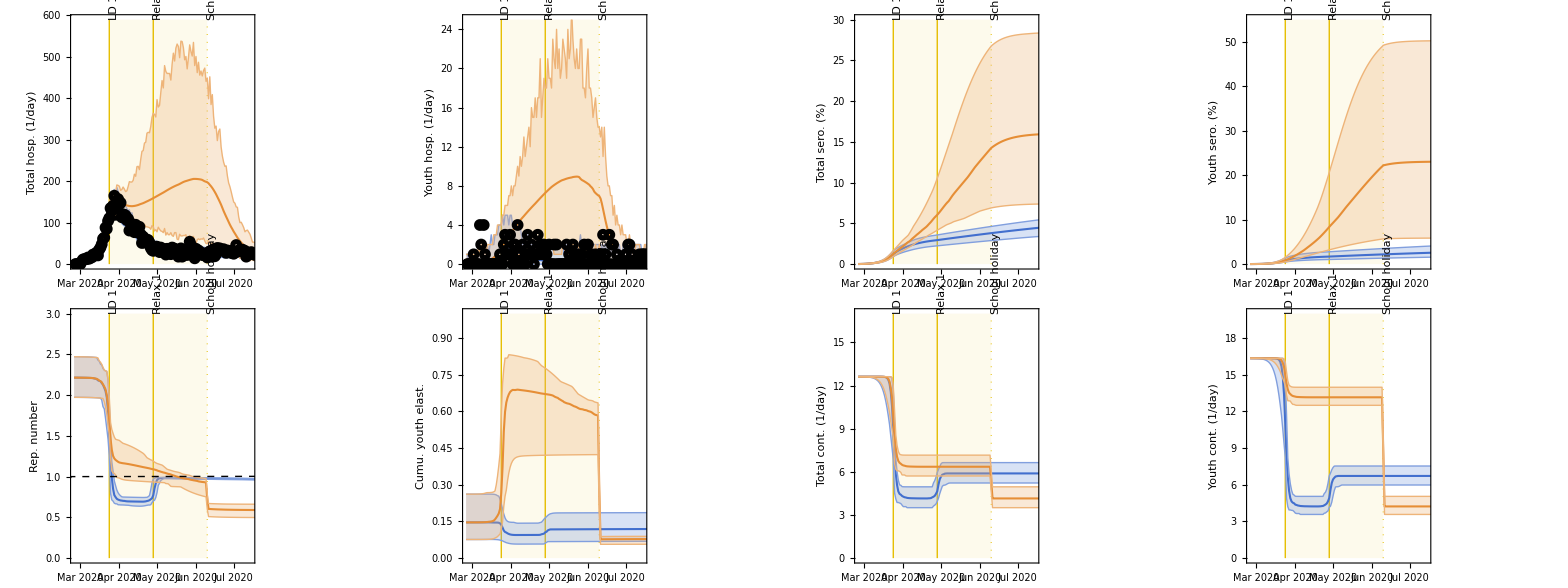
Scenario 1.1
-Graphics-

```mathematica
exportFigs[figGrid4Sens[1],"SFig31"];
```

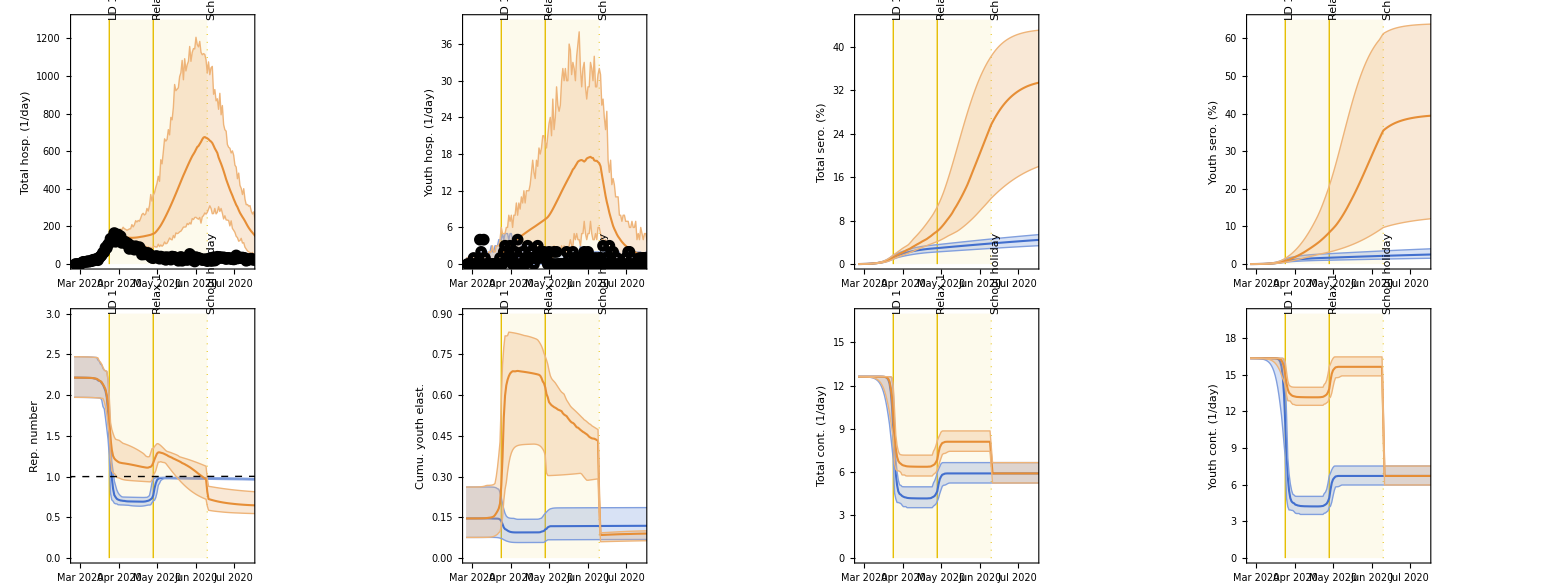
Scenario 1.2
-Graphics-

```mathematica
exportFigs[figGrid4Sens[2],"SFig32"];
```

### Sensitivity analyses for Scenario 2

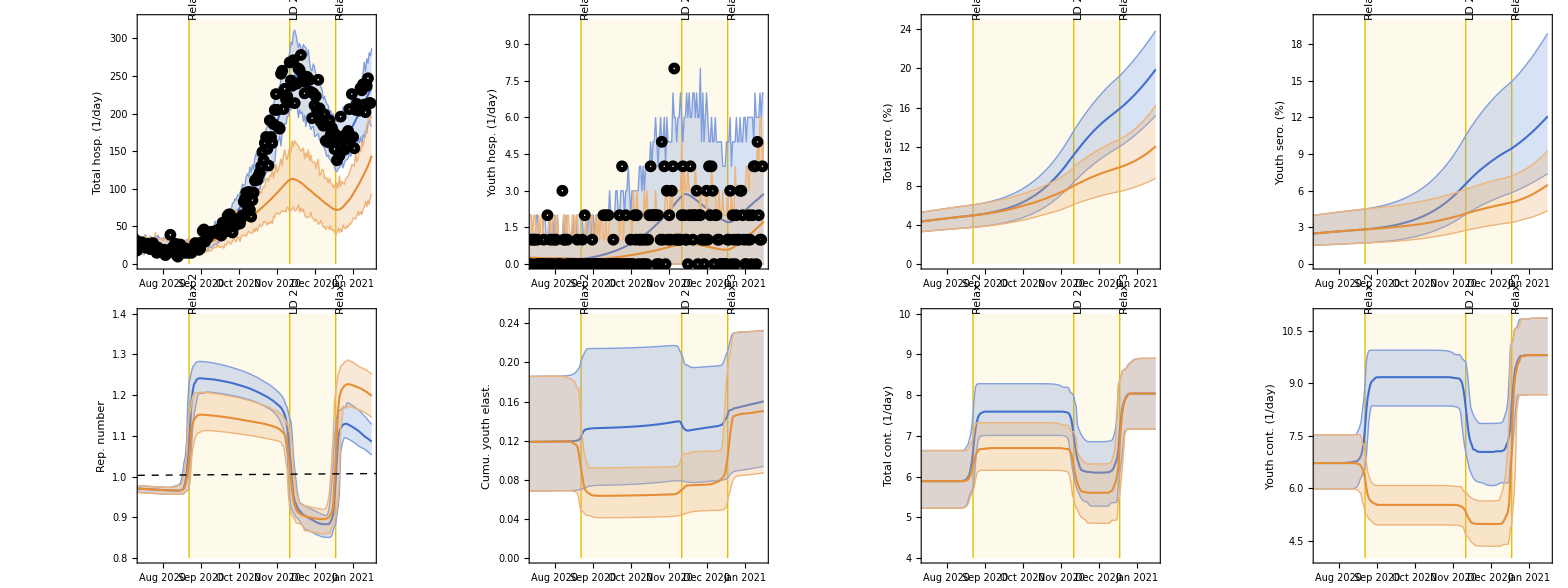
Scenario 2.1
-Graphics-

```mathematica
exportFigs[figGrid4Sens[3],"SFig33"];
```

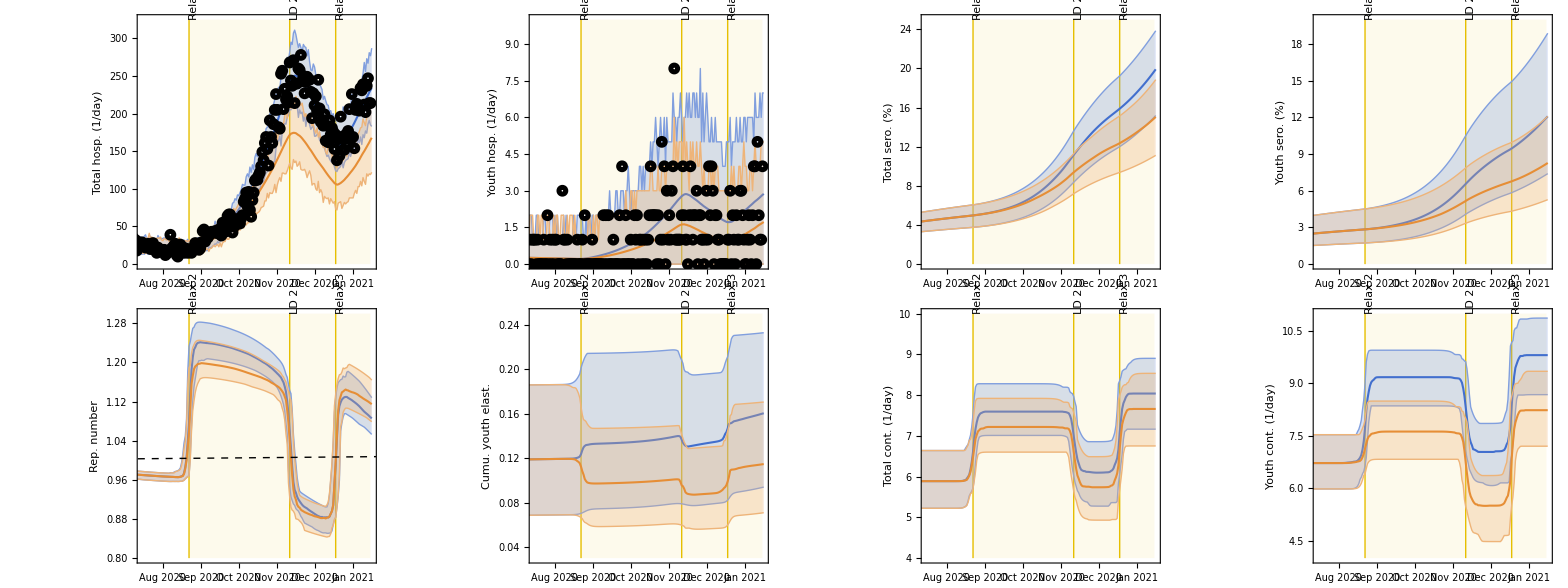
Scenario 2.2
-Graphics-

```mathematica
exportFigs[figGrid4Sens[4],"SFig34"];
```

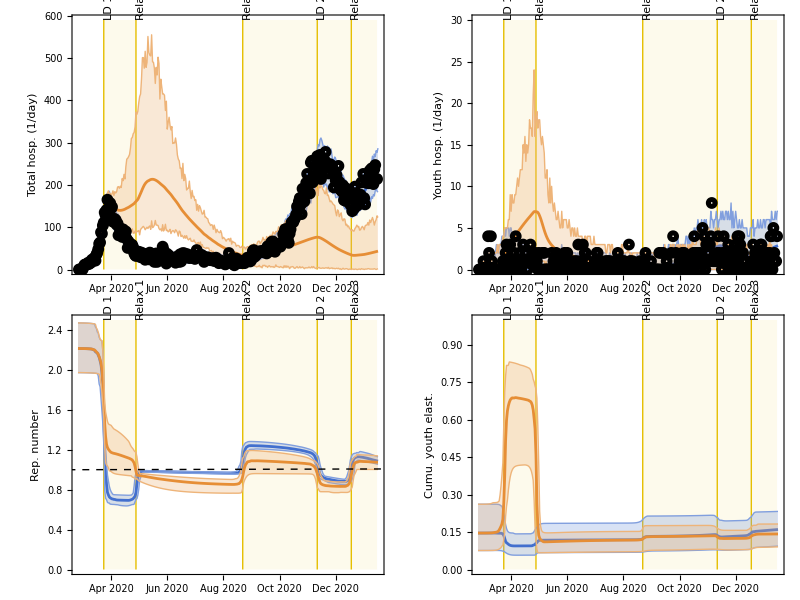
Scenario 2.3
-Graphics-

```mathematica
figHospTotal1to2 =
plotWithLetter[{plotLineWithCrI[hospSimulTotal2Plot[[1]],colorBlue,"","","Total hosp. (1/day)",3,ticksInvisible,{0, 590},0.3,500,Solid,hospTot2Plot[[1]], False],
plotLineWithCrI[hospSimulTotal2Plot[[2]],colorOrange,"","","",3,ticksInvisible,{0, 590},0.3,500,Solid,hospTot2Plot[[2]], False],scatterPlotHospData}, "a", "righter"];

figHospYouth1to2 =
plotWithLetter[{plotLineWithCrI[hospSimulYouth2Plot[[1]],colorBlue,"","","Youth hosp. (1/day)",3,ticksInvisible,{0, 30},0.3,500,Solid,hospYouth2Plot[[1]], False],
plotLineWithCrI[hospSimulYouth2Plot[[2]],colorOrange,"","","",3,ticksInvisible,{0, 30},0.3,500,Solid,hospYouth2Plot[[2]], False],scatterPlotHospDataChild}, "b", "righter"];

figRt1to2 =
plotWithLetter[{plotLineWithCrI[Rt2Plot[[1]],colorBlue,"","","Rep. number",3,ticksVisible,{0, 2.5},0.3,500,Solid, {},False],
plotLineWithCrI[Rt2Plot[[2]],colorOrange,"","","",3, ticksVisible,{0, 2.5},0.3,500,Solid,{}, False],Rt1Line}, "c", "righter"];

figCumuElas1to2 =
plotWithLetter[{plotLineWithCrI[cumuElas2Plot[[1]],colorBlue,"","","Cumu. youth elast.",3,ticksVisible,{0, 1},0.3,500,Solid, {},False],
plotLineWithCrI[cumuElas2Plot[[2]],colorOrange,"","","",3, ticksVisible,{0, 1},0.3,500,Solid,{}, False]}, "d", "righter"];


figScenario1to2 = Grid[{{Style["Scenario 2.3",TextAlignment -> Center,Black,sizeFontBig, FontFamily->"Helvetica"]},{Grid[{{figHospTotal1to2,figHospYouth1to2},
{figRt1to2,figCumuElas1to2}}]},
{legendRawScen2HospFlat}}];
exportFigs[figScenario1to2, "SFig35"];
```

### Tables

```mathematica
(*Change time index to May 1 (36+30 days of April)*)
timeIndex1=66;

(*Update the row labels to reflect May 1*)
dataTableLabels1May={"Total, hosp cumu","Total, hosp peak val. (<2021)","Total, hosp peak date (<2021)","Youth, hosp cumu","Youth, hosp peak val. (<2021)","Youth, hosp peak date (<2021)","Total, sero end","Youth, sero end","Total, conts May 1","Youth, conts May 1","Rep no, May 1","Youth elas, May 1"};
```

```mathematica
scen1Idx={1,2};

(*Recalculate the snapshot metrics for May 1*)
aveContsScen1Total=Table[getAroundMedian[averageContactsTotal[[scen1Idx[[scenIdx]],All,timeIndex1]]],{scenIdx,1,Length[scen1Idx]}];
aveContsScen1Youth=Table[getAroundMedian[averageContactsYouth[[scen1Idx[[scenIdx]],All,timeIndex1]]],{scenIdx,1,Length[scen1Idx]}];
RtScen1=Table[getAroundMedian[RtScenarios[[scen1Idx[[scenIdx]],All,timeIndex1,1]]],{scenIdx,1,Length[scen1Idx]}];
cumuElasScen1Youth=Table[getAroundMedian[cumuElasGroupedScenarios[[scen1Idx[[scenIdx]],All,timeIndex1,1]]],{scenIdx,1,Length[scen1Idx]}];

(*Recompile the Original Summary*)
scenario1SummaryMay={hospAbsScen1TotalGrouped[[1,{1,2}]],hospScen1PeakValTotal,hospScen1PeakDateTotal,hospAbsScen1TotalGrouped[[2,{1,2}]],hospScen1PeakValYouth,hospScen1PeakDateYouth,seroScen1Total,seroScen1Youth,aveContsScen1Total,aveContsScen1Youth,RtScen1,cumuElasScen1Youth};

dataTableFormatted1May=MapIndexed[formatItem[#1,#2[[1]]]&,scenario1SummaryMay,{2}];
```

```mathematica
scen1SensIdx={1,2};
scen2SensIdx={3,4};
scen23OrigIdx=2;

hospMatrices4Sens={hospitalizationScenariosGrouped4Sens,hospitalizationScenariosTotal4Sens,hospitalizationSimulatedScenariosGrouped4Sens,hospitalizationSimulatedScenariosTotal4Sens};

hospPeakResults4Sens1=getPeaks[#,"Scenario 1"]&/@hospMatrices4Sens;
hospPeakResults4Sens2=getPeaks[#,"Scenario 2"]&/@hospMatrices4Sens;
```

```mathematica
hospAbsScen1SensTotalGrouped={Table[getAroundMedian[Total[hospitalizationScenariosTotal4Sens[[scen1SensIdx[[scenIdx]],1,All,1;;timeEnd1]],{2}]],{scenIdx,1,Length[scen1SensIdx]}],Table[getAroundMedian[Total[hospitalizationScenariosGrouped4Sens[[scen1SensIdx[[scenIdx]],1,All,1;;timeEnd1]],{2}]],{scenIdx,1,Length[scen1SensIdx]}]};

hospAbsScen2SensTotalGrouped={Table[getAroundMedian[Total[hospitalizationScenariosTotal4Sens[[scen2SensIdx[[scenIdx]],1,All,1;;timeEnd2]],{2}]],{scenIdx,1,Length[scen2SensIdx]}],Table[getAroundMedian[Total[hospitalizationScenariosGrouped4Sens[[scen2SensIdx[[scenIdx]],1,All,1;;timeEnd2]],{2}]],{scenIdx,1,Length[scen2SensIdx]}]};

hospAbsScen23TotalGrouped={Table[getAroundMedian[Total[hospitalizationScenariosTotal[[scen23OrigIdx,1,All,1;;timeEnd2]],{2}]],{1}],Table[getAroundMedian[Total[hospitalizationScenariosGrouped[[scen23OrigIdx,1,All,1;;timeEnd2]],{2}]],{1}]};
```

```mathematica
(*Hospitalization Peaks*)hospScen1SensPeakValTotal=Table[getAroundMedian[hospPeakResults4Sens1[[2]][[1,scen1SensIdx[[scenIdx]],1,All]],hospPeakResults4Sens1[[4]][[1,scen1SensIdx[[scenIdx]],1,All]]],{scenIdx,1,Length[scen1SensIdx]}];
hospScen1SensPeakDateTotal=Table[getAroundMedian[hospPeakResults4Sens1[[2]][[2,scen1SensIdx[[scenIdx]],1,All]],hospPeakResults4Sens1[[4]][[2,scen1SensIdx[[scenIdx]],1,All]]],{scenIdx,1,Length[scen1SensIdx]}];
hospScen1SensPeakValYouth=Table[getAroundMedian[hospPeakResults4Sens1[[1]][[1,scen1SensIdx[[scenIdx]],1,All]],hospPeakResults4Sens1[[3]][[1,scen1SensIdx[[scenIdx]],1,All]]],{scenIdx,1,Length[scen1SensIdx]}];
hospScen1SensPeakDateYouth=Table[getAroundMedian[hospPeakResults4Sens1[[1]][[2,scen1SensIdx[[scenIdx]],1,All]],hospPeakResults4Sens1[[3]][[2,scen1SensIdx[[scenIdx]],1,All]]],{scenIdx,1,Length[scen1SensIdx]}];

hospScen2SensPeakValTotal=Table[getAroundMedian[hospPeakResults4Sens2[[2]][[1,scen2SensIdx[[scenIdx]],1,All]],hospPeakResults4Sens2[[4]][[1,scen2SensIdx[[scenIdx]],1,All]]],{scenIdx,1,Length[scen2SensIdx]}];
hospScen2SensPeakDateTotal=Table[getAroundMedian[hospPeakResults4Sens2[[2]][[2,scen2SensIdx[[scenIdx]],1,All]],hospPeakResults4Sens2[[4]][[2,scen2SensIdx[[scenIdx]],1,All]]],{scenIdx,1,Length[scen2SensIdx]}];
hospScen2SensPeakValYouth=Table[getAroundMedian[hospPeakResults4Sens2[[1]][[1,scen2SensIdx[[scenIdx]],1,All]],hospPeakResults4Sens2[[3]][[1,scen2SensIdx[[scenIdx]],1,All]]],{scenIdx,1,Length[scen2SensIdx]}];
hospScen2SensPeakDateYouth=Table[getAroundMedian[hospPeakResults4Sens2[[1]][[2,scen2SensIdx[[scenIdx]],1,All]],hospPeakResults4Sens2[[3]][[2,scen2SensIdx[[scenIdx]],1,All]]],{scenIdx,1,Length[scen2SensIdx]}];

(*Seroprevalence*)
seroScen1SensTotal=Table[getAroundMedian[seroprevalenceScenariosTotal4Sens[[scen1SensIdx[[scenIdx]],1,All,timeEnd1]]],{scenIdx,1,Length[scen1SensIdx]}];
seroScen1SensYouth=Table[getAroundMedian[seroprevalenceScenariosGrouped4Sens[[scen1SensIdx[[scenIdx]],1,All,timeEnd1]]],{scenIdx,1,Length[scen1SensIdx]}];

seroScen2SensTotal=Table[getAroundMedian[seroprevalenceScenariosTotal4Sens[[scen2SensIdx[[scenIdx]],1,All,timeEnd2]]],{scenIdx,1,Length[scen2SensIdx]}];
seroScen2SensYouth=Table[getAroundMedian[seroprevalenceScenariosGrouped4Sens[[scen2SensIdx[[scenIdx]],1,All,timeEnd2]]],{scenIdx,1,Length[scen2SensIdx]}];

(*Average Contacts*)
aveContsScen1SensTotal=Table[getAroundMedian[averageContactsTotal4Sens[[scen1SensIdx[[scenIdx]],All,timeIndex1]]],{scenIdx,1,Length[scen1SensIdx]}];
aveContsScen1SensYouth=Table[getAroundMedian[averageContactsYouth4Sens[[scen1SensIdx[[scenIdx]],All,timeIndex1]]],{scenIdx,1,Length[scen1SensIdx]}];

aveContsScen2SensTotal=Table[getAroundMedian[averageContactsTotal4Sens[[scen2SensIdx[[scenIdx]],All,timeIndex2]]],{scenIdx,1,Length[scen2SensIdx]}];
aveContsScen2SensYouth=Table[getAroundMedian[averageContactsYouth4Sens[[scen2SensIdx[[scenIdx]],All,timeIndex2]]],{scenIdx,1,Length[scen2SensIdx]}];

(*Reproduction Number& Elasticity*)
RtScen1Sens=Table[getAroundMedian[RtScenarios4Sens[[scen1SensIdx[[scenIdx]],All,timeIndex1,1]]],{scenIdx,1,Length[scen1SensIdx]}];
cumuElasScen1SensYouth=Table[getAroundMedian[cumuElasGroupedScenarios4Sens[[scen1SensIdx[[scenIdx]],All,timeIndex1,1]]],{scenIdx,1,Length[scen1SensIdx]}];

RtScen2Sens=Table[getAroundMedian[RtScenarios4Sens[[scen2SensIdx[[scenIdx]],All,timeIndex2,1]]],{scenIdx,1,Length[scen2SensIdx]}];
cumuElasScen2SensYouth=Table[getAroundMedian[cumuElasGroupedScenarios4Sens[[scen2SensIdx[[scenIdx]],All,timeIndex2,1]]],{scenIdx,1,Length[scen2SensIdx]}];
```

```mathematica
scenario1SensSummaryMay={hospAbsScen1SensTotalGrouped[[1,All]],hospScen1SensPeakValTotal,hospScen1SensPeakDateTotal,hospAbsScen1SensTotalGrouped[[2,All]],hospScen1SensPeakValYouth,hospScen1SensPeakDateYouth,seroScen1SensTotal,seroScen1SensYouth,aveContsScen1SensTotal,aveContsScen1SensYouth,RtScen1Sens,cumuElasScen1SensYouth};

dataTableFormatted1SensMay=MapIndexed[formatItem[#1,#2[[1]]]&,scenario1SensSummaryMay,{2}];
(*Thread all 5 columns together*)dataTableFinalCombined=MapThread[List,{dataTableLabels1May,dataTableFormatted1May[[All,1]],(*Baseline 1*)dataTableFormatted1May[[All,2]],(*Original Scenario 1*)dataTableFormatted1SensMay[[All,1]],(*Scenario 1.1*)dataTableFormatted1SensMay[[All,2]]  (*Scenario 1.2*)}];

(*Apply column headings*)
columnHeadingsCombined={"Model outcome","Baseline 1","Orig. Scenario 1","Scenario 1.1","Scenario 1.2"};

TableForm[dataTableFinalCombined,TableHeadings->{None,columnHeadingsCombined}]
```

Model outcome | Baseline 1 | Orig. Scenario 1 | Scenario 1.1 | Scenario 1.2
Total, hosp cumu | 6452 (6161 - 6706) | 18283 (12379 - 31854) | 18027 (9173 - 33136) | 40472 (22393 - 60484)
Total, hosp peak val. (<2021) | 143 (126 - 169) | 213 (120 - 563) | 206 (124 - 548) | 695 (283 - 1190)
Total, hosp peak date (<2021) | Mar 29 (Mar 25 - Apr 02) | May 14 (Mar 27 - May 26) | May 26 (Mar 31 - Jun 14) | Jun 11 (May 24 - Jun 22)
Youth, hosp cumu | 68 (46 - 81) | 355 (200 - 624) | 613 (246 - 1103) | 986 (450 - 1536)
Youth, hosp peak val. (<2021) | 2 (1 - 4) | 7 (2 - 19) | 9 (1 - 25) | 19 (4 - 33)
Youth, hosp peak date (<2021) | Mar 27 (Mar 16 - May 08) | Apr 28 (Apr 07 - May 09) | May 17 (Apr 24 - Jun 05) | Jun 06 (May 14 - Jun 18)
Total, sero end | 4.40 (3.35 - 5.35) | 13.89 (8.47 - 22.44) | 15.88 (7.36 - 28.32) | 33.16 (17.62 - 42.94)
Youth, sero end | 2.52 (1.54 - 4.02) | 13.19 (4.98 - 29.95) | 23.01 (5.85 - 50.21) | 39.34 (11.93 - 63.75)
Total, conts May 1 | 5.49 (4.48 - 6.36) | 6.01 (5.26 - 6.87) | 6.35 (5.71 - 7.16) | 7.69 (6.69 - 8.56)
Youth, conts May 1 | 6.15 (4.58 - 7.22) | 8.34 (6.44 - 13.35) | 13.15 (12.50 - 13.98) | 15.07 (13.50 - 16.15)
Rep no, May 1 | 0.92 (0.74 - 0.99) | 0.94 (0.90 - 1.06) | 1.08 (0.93 - 1.17) | 1.25 (1.07 - 1.39)
Youth elas, May 1 | 0.11 (0.07 - 0.17) | 0.18 (0.07 - 0.58) | 0.67 (0.42 - 0.77) | 0.59 (0.30 - 0.71)

```mathematica
scenario2SensSummary={hospAbsScen2SensTotalGrouped[[1,All]],hospScen2SensPeakValTotal,hospScen2SensPeakDateTotal,hospAbsScen2SensTotalGrouped[[2,All]],hospScen2SensPeakValYouth,hospScen2SensPeakDateYouth,seroScen2SensTotal,seroScen2SensYouth,aveContsScen2SensTotal,aveContsScen2SensYouth,RtScen2Sens,cumuElasScen2SensYouth};

scenario23Summary={hospAbsScen23TotalGrouped[[1,All]],Table[getAroundMedian[hospPeakResults2[[2]][[1,scen23OrigIdx,1,All]],hospPeakResults2[[4]][[1,scen23OrigIdx,1,All]]],{1}],Table[getAroundMedian[hospPeakResults2[[2]][[2,scen23OrigIdx,1,All]],hospPeakResults2[[4]][[2,scen23OrigIdx,1,All]]],{1}],hospAbsScen23TotalGrouped[[2,All]],Table[getAroundMedian[hospPeakResults2[[1]][[1,scen23OrigIdx,1,All]],hospPeakResults2[[3]][[1,scen23OrigIdx,1,All]]],{1}],Table[getAroundMedian[hospPeakResults2[[1]][[2,scen23OrigIdx,1,All]],hospPeakResults2[[3]][[2,scen23OrigIdx,1,All]]],{1}],Table[getAroundMedian[seroprevalenceScenariosTotal[[scen23OrigIdx,1,All,timeEnd2]]],{1}],Table[getAroundMedian[seroprevalenceScenariosGrouped[[scen23OrigIdx,1,All,timeEnd2]]],{1}],Table[getAroundMedian[averageContactsTotal[[scen23OrigIdx,All,timeIndex2]]],{1}],Table[getAroundMedian[averageContactsYouth[[scen23OrigIdx,All,timeIndex2]]],{1}],Table[getAroundMedian[RtScenarios[[scen23OrigIdx,All,timeIndex2,1]]],{1}],Table[getAroundMedian[cumuElasGroupedScenarios[[scen23OrigIdx,All,timeIndex2,1]]],{1}]};

dataTableFormatted2Sens=MapIndexed[formatItem[#1,#2[[1]]]&,scenario2SensSummary,{2}];
dataTableFormatted23=MapIndexed[formatItem[#1,#2[[1]]]&,scenario23Summary,{2}];
dataTableFinalPhase2Combined=MapThread[List,{dataTableLabels2,dataTableFormatted2[[All,1]],(*Baseline 2*)dataTableFormatted2Sens[[All,1]],(*Scenario 2.1*)dataTableFormatted2Sens[[All,2]],(*Scenario 2.2*)dataTableFormatted23[[All,1]]        (*Scenario 2.3 (Orig Scen 1 into Phase 2)*)}];

columnHeadingsPhase2={"Model outcome","Baseline 2","Scenario 2.1","Scenario 2.2","Scenario 2.3"};

TableForm[dataTableFinalPhase2Combined,TableHeadings->{None,columnHeadingsPhase2}]
```

Model outcome | Baseline 2 | Scenario 2.1 | Scenario 2.2 | Scenario 2.3
Total, hosp cumu | 21507 (20955 - 22075) | 17986 (15354 - 20295) | 22258 (20272 - 23790) | 28650 (25153 - 35579)
Total, hosp peak val. (<2021) | 251 (227 - 286) | 114 (75 - 148) | 175 (139 - 206) | 89 (53 - 204)
Total, hosp peak date (<2021) | Nov 15 (Nov 08 - Nov 24) | Nov 14 (Nov 05 - Nov 24) | Nov 15 (Nov 06 - Nov 25) | Jul 15 (Jul 07 - Nov 14)
Youth, hosp cumu | 245 (200 - 292) | 166 (135 - 197) | 215 (182 - 246) | 448 (347 - 658)
Youth, hosp peak val. (<2021) | 3 (2 - 6) | 1 (0 - 3) | 2 (0 - 3) | 1 (0 - 4)
Youth, hosp peak date (<2021) | Nov 14 (Oct 12 - Dec 07) | Nov 15 (Sep 28 - Dec 07) | Nov 13 (Oct 19 - Dec 05) | Nov 09 (Jul 17 - Dec 11)
Total, sero end | 19.57 (14.93 - 23.49) | 11.83 (8.65 - 15.88) | 14.82 (10.97 - 18.53) | 20.06 (17.48 - 23.96)
Youth, sero end | 11.87 (7.27 - 18.56) | 6.35 (4.27 - 9.05) | 8.14 (5.19 - 11.90) | 16.61 (9.24 - 30.57)
Total, conts Sep 1 | 7.59 (7.01 - 8.28) | 6.68 (6.15 - 7.32) | 7.19 (6.60 - 7.92) | 7.59 (7.01 - 8.28)
Youth, conts Sep 1 | 9.17 (8.36 - 9.95) | 5.54 (4.95 - 6.08) | 7.59 (6.83 - 8.50) | 9.17 (8.36 - 9.95)
Rep no, Sep 1 | 1.24 (1.20 - 1.28) | 1.15 (1.11 - 1.21) | 1.20 (1.17 - 1.25) | 1.09 (0.96 - 1.19)
Youth elas, Sep 1 | 0.13 (0.07 - 0.21) | 0.06 (0.04 - 0.09) | 0.10 (0.06 - 0.15) | 0.13 (0.08 - 0.18)